# Code for “Dynamics of thyroid diseases and thyroid-axis gland masses”

```mathematica
SetDirectory["C:\\Users\\yaelko\\Box\\hpt axis\\2021\\paper figures"]
```

C:\Users\yaelko\Box\hpt axis\2021\paper figures

## Model definition

The model dynamics are defined by the following equations:
x1'[t]==(b1 u)/x3[t]-a1 x1[t]
x2'[t]==(b2 P[t] x1[t])/x3[t]-a2 x2[t]
x3'[t]==b30+b3 T[t] ((Ab+x2[t])/(1+kx2 (Ab+x2[t])))-a3 x3[t]
T'[t]==T[t] (bt (1-kT T[t]) ((Ab+x2[t])/(1+kx2 (Ab+x2[t])))-at)
P'[t]==P[t] ((bp (1-kP P[t]))/x3[t]-ap)

Variables are:
x1 = TRH concentration
x2 = TSH concentration
x3 = TH concentration
T = thyroid gland volume
P = pituitary gland volume

Parameters are:
u = environmental input
a1, a2, a3 = TRH, TSH, TH removal rate respectively.
at, ap = thyroid/pituitary cell removal rate, respectively.
b1, b2, b3 = TRH, TSH, TH production rate, respectively
bt, bp = thyroid/pituitary cell proliferation rate, respectively
kP, kT = carrying capacity terms for the thyroid/pituitary gland respectively. Note that this terms appear in an inverse form so that when kT=0, kP=0, this mean that the glands do not have carrying capacities and can grow indefenitely. Under normal conditions, both glands are far fro their 		carrying capacitites, and hence kT≅kP≅0. When modeling Hashimoto’s thyroiditis, the relevant carrying capacity is that of the pituitary gland (because the thyroid gland is destructed and is thus small), therefore we approximate kT~0. When modeling Graves’disease, the relevant 			carrying capacity is that of the thyroid gland (the pituitary is small due to the negative TH feedback), therefore  we approximate kP~0.
Ab = TSH-receptor stimulating antibodies. We use this term when modeling Grave’s disease. Under normal conditions Ab = 0.
b30 = External thyroid hormone supply. We use this term when simulating levothyroxine treatment of Hashimoto’s thyroidits. Under normal conditions b30 = 0.
kx2 = Michaelis-Menten coefficient for the response function of TH. This parameter served us to explore the effect of using a MM response function for TH, which is more realistic than a linear function. 
	We found that this choice does not affect the qualitative results of the model, thus we set kx2=0

Parameter estimation:
Half life times:
TRH: 6 minutes = (1/24/60)*6 =  0.004 days
TSH: 1 hour = (1/24) = 0.04 days
T4: 1 week = 7 days
Glands: ~ 1 month = 30 days
Production rates were chosen so that in the simple model that represents the healthy state, the variables steady state is equal to 1: x1=1, x2=1, x3=1,T=1, P=1

## Steady State - simple model

```mathematica
With[{vars={x1,x2,x3,T,P},u=1,a1=250.,b1=250.,a2=25.,b2=25.,a3=1/7,b3=1/7,kx2=0,Ab=0,kT=0,at=1/30,bt=1/30,kP=0,ap=1/30,bp=1/30},
Flatten@{stst=NSolve[{0==-a1 x1+(b1 u)/x3,0==-a2 x2+(b2 P x1)/x3,0==b3 T ((Ab+x2)/(1+kx2 x2))-a3 x3,0==T (-at+bt (1-kT T) ((Ab+x2)/(1+kx2 x2))),0==P (-ap+(bp (1-kP P))/x3)},vars,Reals]
}
]
```

{x3→1.,x1→1.,x2→1.,T→1.,P→1.}

```mathematica
NSolve[{0==-a1 x1+(b1 u)/x3,0==-a2 x2+(b2 P x1)/x3,0==b3 T x2-a3 x3,0==T (-at+bt  x2),0==P (-ap+bp/x3)},{x1,x2,x3,T,P},Reals]
```

{{x1→(ap b1 u)/(a1 bp),x2→at/bt,x3→bp/ap,T→(a3 bp bt)/(ap at b3),P→(a1 a2 at bp^2)/(ap^2 b1 b2 bt u)}}

## Simulations

```mathematica
dyn=ParametricNDSolveValue[{x1'[t]==-a1 x1[t]+(b1 u)/x3[t],x1[0]== x11,
x2'[t]==-a2 x2[t]+(b2 P[t] x1[t])/x3[t],x2[0]== x20,
x3'[t]==b30+b3 T[t] ((Ab+x2[t])/(1+kx2 (Ab+x2[t])))-a3 x3[t],x3[0]== x30,
T'[t]==T[t] (-at+bt (1-kT T[t]) ((Ab+x2[t])/(1+kx2 (Ab+x2[t])))),T[0]== T0,
P'[t]==P[t] (-ap+(bp (1-kP P[t]))/x3[t]),P[0]== P0
},
{ x1[t],x2[t],x3[t],T[t],P[t]},{t,0,100000},{b30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,at,bt,kP,ap,bp,x11,x20,x30,T0,P0}]
```

ParametricFunction[<>]

#### Exact adaptation to a step in b3 (reduction in iodine consumption)

Gland mass model explains compensation for low iodine and its breakdown in goiter: (A) Simulation of a step reduction of maximal TH production per unit thyroid mass, as occurs in iodine deficiency, in the gland-mass model (without carrying capacities) shows compensation to a euthyroid state: enlarged thyroid, a transient growth in thyrotroph mass and return of hormones to baseline. A model with no gland-mass changes shows hypothyroidism for the same step change (gray lines).

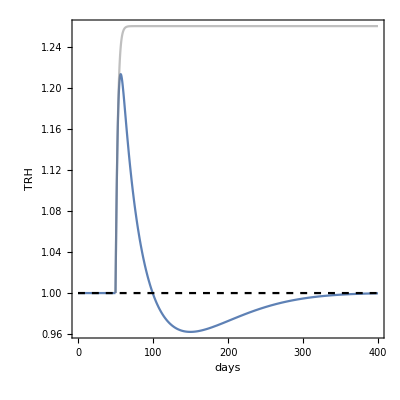
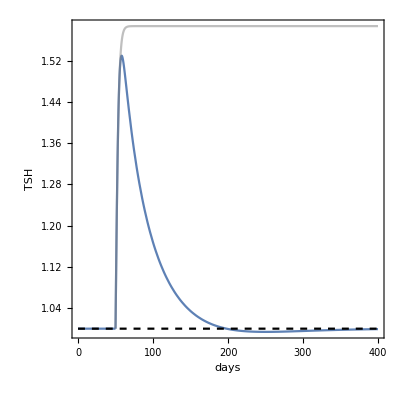
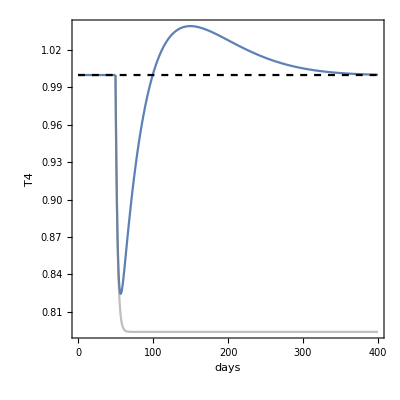
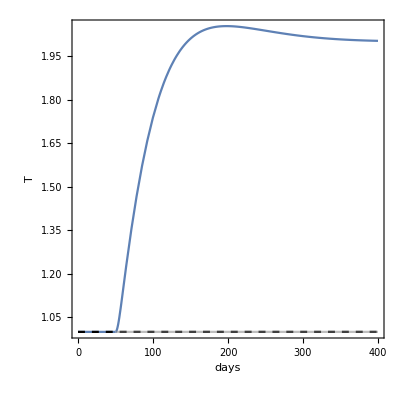
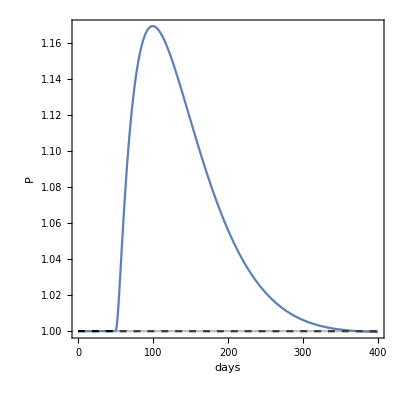
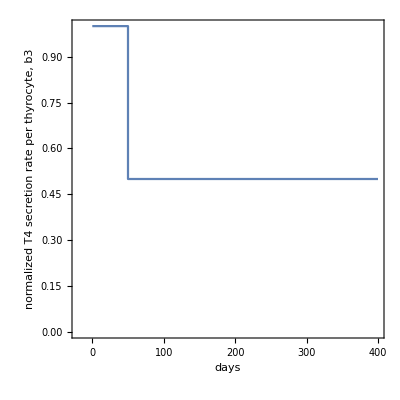

```mathematica
With[{u=1,a1=250.,b1=250.,a2=25.,b2=25.,a3=1/7,b3=1/7,kx2=0,Ab=0,kT=0,at=1/30,bt=1/30,kP=0,ap=1/30,bp=1/30,b30=0,τ=50,tmax=400, leg={ "TRH","TSH","T4","T","P"},vars={x1,x2,x3,T,P}},
Flatten@{stst=NSolve[{0==-a1 x1+(b1 u)/x3,0==-a2 x2+(b2 P x1)/x3,0==b3 T ((Ab+x2)/(1+kx2 x2))-a3 x3,0==T (-at+bt (1-kT T) ((Ab+x2)/(1+kx2 x2))),0==P (-ap+(bp (1-kP P))/x3)},vars,Reals][[1]];
dyn0=Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,at,bt,kP,ap,bp,x1,x2,x3,T,P]/.stst];
Table[
Show[{
ParametricPlot[{t,dyn0[[i]]},{t,0,τ}],
ParametricPlot[{tt+τ,(Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,0.5b3,kx2,Ab,kT,at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[i]])/.t->tt},{tt,0,tmax-τ},AspectRatio->1],
ListLinePlot[{{0,vars[[i]]/.stst},{tmax,vars[[i]]/.stst}},PlotStyle->{Dashed,Black}],
ParametricPlot[{tt+τ,(Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,0.5b3,kx2,Ab,kT,10^-8 at,10^-8 bt,kP,10^-8 ap,10^-8 bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[i]])/.t->tt},{tt,0,tmax-τ},AspectRatio->1,PlotStyle->{Gray,Opacity[0.5]}]
},PlotRange->All,AspectRatio->1,Frame-> True,FrameLabel->{"days",leg[[i]]},AxesOrigin-> {0,0.7}]
,{i,Range[5]}],
ListLinePlot[{{0,1},{τ,1},{τ,0.5},{tmax,0.5}},PlotRange->{{-20,tmax},All},Ticks->{Automatic,{0.5,1}}, Frame->True,FrameLabel->{"days","normalized T4 secretion rate per thyrocyte, b3"},AspectRatio->1]
}
]
```

#### Exact adaptation to a step in b3 (reduction in iodine consumption) - with carrying capacities

(B) Adding carrying capacities to the gland-mass model limits compensation. Simulations show hypothyroidism for a large step reduction in iodine that causes the enlarged thyroid and thyrotroph mass to approach their carrying capacity.

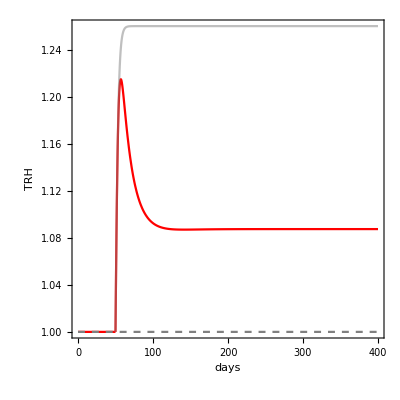
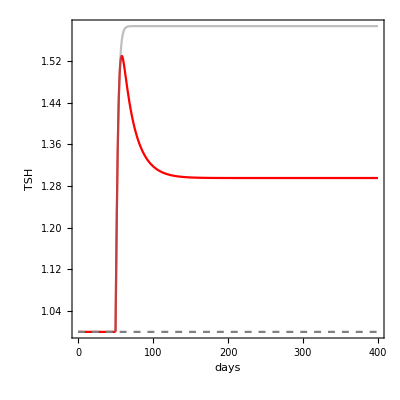
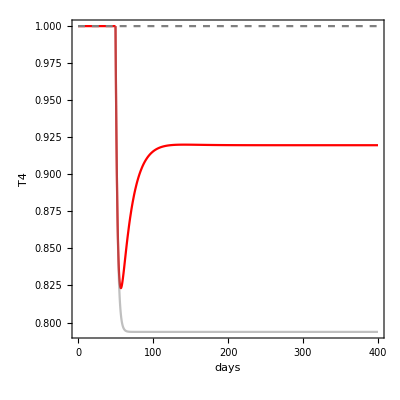
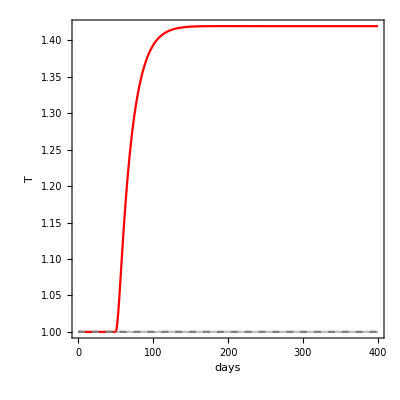
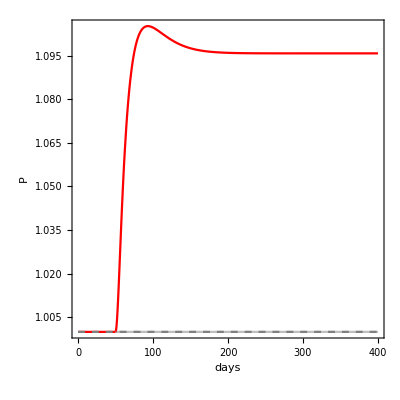
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{u=1,a1=250.,b1=250.,a2=25.,b2=25.,a3=1/7,b3=1/7,kx2=0,Ab=0,kT=1,at=1/30,bt=1/30,kP=1,ap=1/30,bp=1/30,b30=0,τ=50,tmax=400, leg={ "TRH","TSH","T4","T","P"},vars={x1,x2,x3,T,P}},
Flatten@{stst=NSolve[{0==-a1 x1+(b1 u)/x3,0==-a2 x2+(b2 P x1)/x3,0==b3 T ((Ab+x2)/(1+kx2 x2))-a3 x3,0==T (-at+bt (1-kT T) ((Ab+x2)/(1+kx2 x2))),0==P (-ap+(bp (1-kP P))/x3)},vars,Reals][[1]];
dyn0=Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,at,bt,kP,ap,bp,x1,x2,x3,T,P]/.stst];
Table[
Show[{
ParametricPlot[{t,dyn0[[i]]/(vars[[i]]/.stst)},{t,0,τ},PlotStyle->Red],
ParametricPlot[{tt+τ,(1/(vars[[i]]/.stst)Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,0.5b3,kx2,Ab,kT,at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[i]])/.t->tt},{tt,0,tmax-τ},AspectRatio->1,PlotStyle->Red],
ListLinePlot[{{0,1(*vars[[i]]/.stst*)},{tmax,1(*vars[[i]]/.stst*)}},PlotStyle->{Dashed,Gray}],(*st.st line *)
ParametricPlot[{tt+τ,(1/(vars[[i]]/.stst)Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,0.5b3,kx2,Ab,kT,10^-8 at,10^-8 bt,kP,10^-8 ap,10^-8 bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[i]])/.t->tt},{tt,0,tmax-τ},AspectRatio->1,PlotStyle->{Gray,Opacity[0.5]}]
},PlotRange->All,AspectRatio->1,Frame-> True,FrameLabel->{"days",leg[[i]]},AxesOrigin-> {0,0.7}]
,{i,Range[5]}],
ListLinePlot[{{0,1},{τ,1},{τ,0.5},{tmax,0.5}},PlotRange->{{-20,tmax},All},Ticks->{Automatic,{0.5,1}}, Frame->True,FrameLabel->{"days","normalized T4 secretion rate per thyrocyte, b3"},AspectRatio->1]
}
]
```

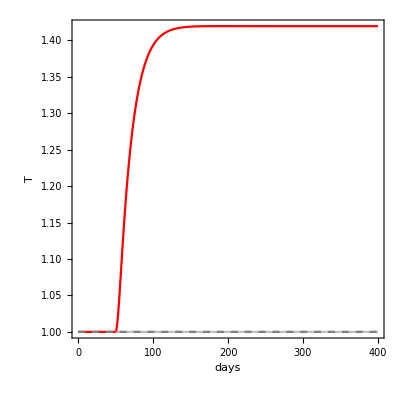
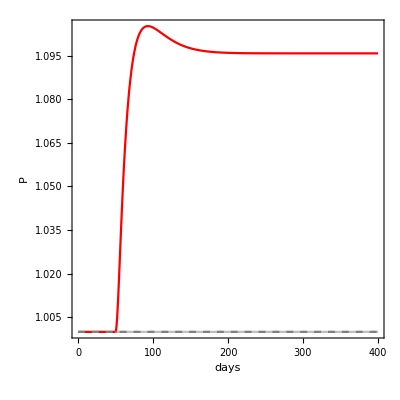
```mathematica
Show[{-Graphics-,-Graphics-},FrameLabel->{"days","T, P"}]
```

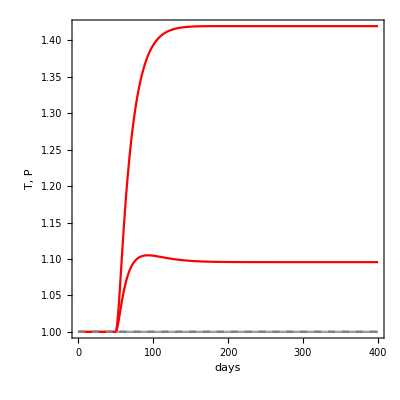

### Thyroidectomy

```mathematica
dynTremoval=ParametricNDSolveValue[{x1'[t]==-a1 x1[t]+(b1 u)/x3[t],x1[0]== x11,
x2'[t]==-a2 x2[t]+(b2 P[t] x1[t])/x3[t],x2[0]== x20,
x3'[t]==b30+b3 T[t] ((Ab+x2[t])/(1+kx2 (Ab+x2[t])))-a3 x3[t],x3[0]== x30,
T[t]== T0,
P'[t]==P[t] (-ap+(bp (1-kP P[t]))/x3[t]),P[0]== P0
},
{ x1[t],x2[t],x3[t],T[t],P[t]},{t,0,100000},{b30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,at,bt,kP,ap,bp,x11,x20,x30,T0,P0}]
```

ParametricFunction[<>]

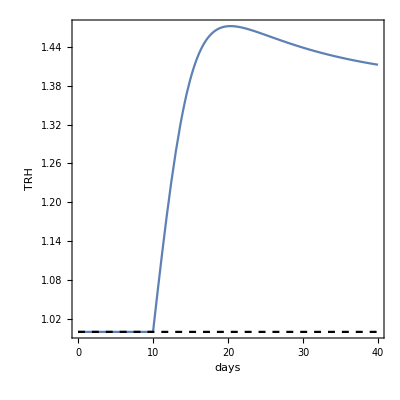
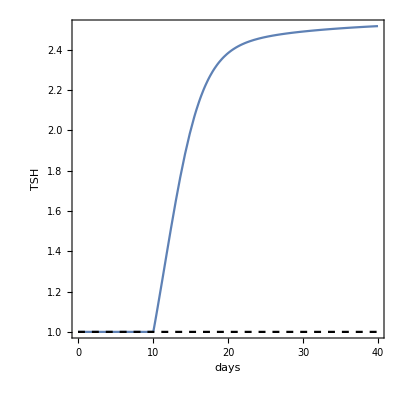
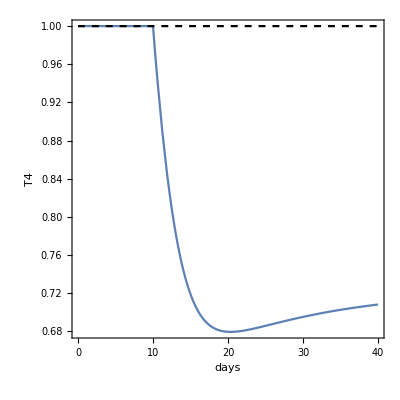
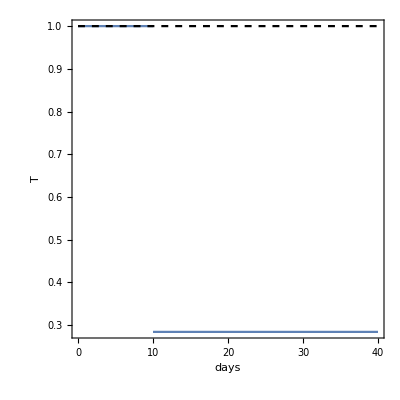
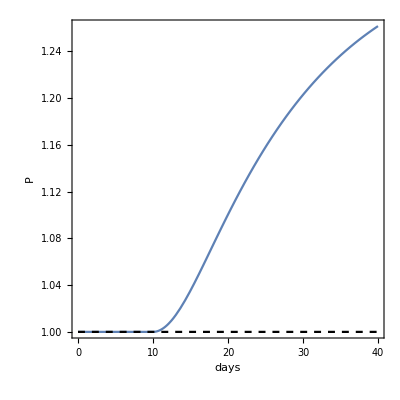

```mathematica
With[{u=1,a1=250.,b1=250.,a2=25.,b2=25.,a3=1/7,b3=1/7,kx2=0,Ab=0,kT=1,at=1/30,bt=1/30,kP=1,ap=1/30,bp=1/30,b30=0,τ=10,tmax=40, leg={ "TRH","TSH","T4","T","P"},vars={x1,x2,x3,T,P}},
Flatten@{stst=NSolve[{0==-a1 x1+(b1 u)/x3,0==-a2 x2+(b2 P x1)/x3,0==b3 T ((Ab+x2)/(1+kx2 x2))-a3 x3,0==T (-at+bt (1-kT T) ((Ab+x2)/(1+kx2 x2))),0==P (-ap+(bp (1-kP P))/x3)},vars,Reals][[1]];
dyn0=Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,at,bt,kP,ap,bp,x1,x2,x3,T,P]/.stst];
Table[
Show[{
ParametricPlot[{t,dyn0[[i]]/(vars[[i]]/.stst)},{t,0,τ}],
ParametricPlot[{tt+τ,(1/(vars[[i]]/.stst)Evaluate[dynTremoval[b30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],0.1,#[[5]]]&@(dyn0/.t->τ)][[i]])/.t->tt},{tt,0,tmax-τ},AspectRatio->1],
ListLinePlot[{{0,1},{tmax,1}},PlotStyle->{Dashed,Black}]
},PlotRange->All,AspectRatio->1,Frame-> True,FrameLabel->{"days",leg[[i]]},AxesOrigin-> {0,0.7}]
,{i,Range[5]}]
}
]
```

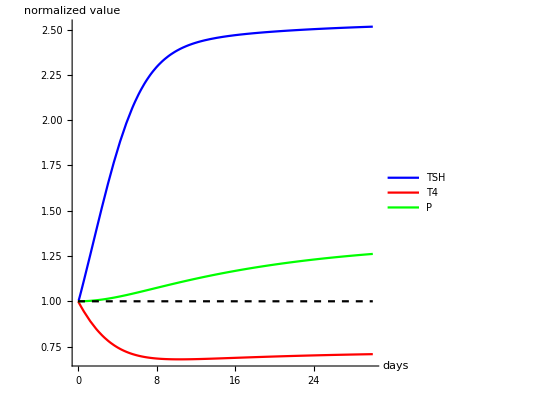

```mathematica
With[{u=1,a1=250.,b1=250.,a2=25.,b2=25.,a3=1/7,b3=1/7,kx2=0,Ab=0,kT=1,at=1/30,bt=1/30,kP=1,ap=1/30,bp=1/30,b30=0,τ=0.01,tmax=30, leg={ "TRH","TSH","T4","T","P"},vars={x1,x2,x3,T,P}},
Flatten@{stst=NSolve[{0==-a1 x1+(b1 u)/x3,0==-a2 x2+(b2 P x1)/x3,0==b3 T ((Ab+x2)/(1+kx2 x2))-a3 x3,0==T (-at+bt (1-kT T) ((Ab+x2)/(1+kx2 x2))),0==P (-ap+(bp (1-kP P))/x3)},vars,Reals][[1]];
dyn0=Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,at,bt,kP,ap,bp,x1,x2,x3,T,P]/.stst];
Show[
With[{i=2},Show[{
ParametricPlot[{t,dyn0[[i]]/(vars[[i]]/.stst)},{t,0,τ},PlotStyle-> Blue],
ParametricPlot[{tt+τ,(1/(vars[[i]]/.stst)Evaluate[dynTremoval[b30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],0.1,#[[5]]]&@(dyn0/.t->τ)][[i]])/.t->tt},{tt,0,tmax-τ},AspectRatio->1,PlotStyle-> Blue, PlotLegends-> LineLegend[{Blue,Red,Green},{"TSH","T4","P"}]]
},PlotRange->All,AspectRatio->1,AxesLabel->{"days","normalized value"},AxesOrigin-> {0,0}]],
With[{i=3},Show[{
ParametricPlot[{t,dyn0[[i]]/(vars[[i]]/.stst)},{t,0,τ},PlotStyle-> Red],
ParametricPlot[{tt+τ,(1/(vars[[i]]/.stst)Evaluate[dynTremoval[b30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],0.1,#[[5]]]&@(dyn0/.t->τ)][[i]])/.t->tt},{tt,0,tmax-τ},AspectRatio->1,PlotStyle-> Red]
},PlotRange->All,AspectRatio->1,AxesOrigin-> {0,0}]],
With[{i=5},Show[{
ParametricPlot[{t,dyn0[[i]]/(vars[[i]]/.stst)},{t,0,τ},PlotStyle->Green],
ParametricPlot[{tt+τ,(1/(vars[[i]]/.stst)Evaluate[dynTremoval[b30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],0.1,#[[5]]]&@(dyn0/.t->τ)][[i]])/.t->tt},{tt,0,tmax-τ},AspectRatio->1,PlotStyle->Green]
},PlotRange->All,AspectRatio->1,AxesOrigin-> {0,0}]],
ListLinePlot[{{0,1},{tmax,1}},PlotStyle->{Dashed,Black}]
]
}
]
```

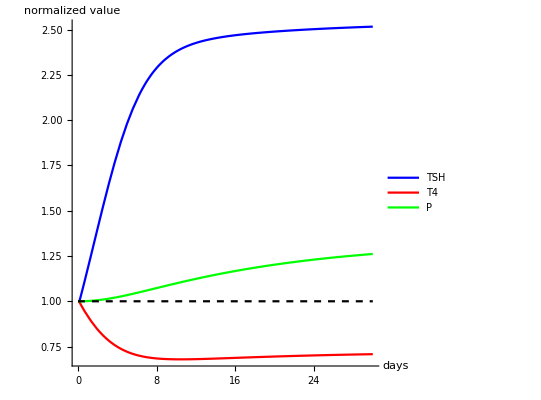
```mathematica
Export["thyroidectomy_simulation.pdf",{-Graphics-}]
```

thyroidectomy_simulation.pdf

#### Hysteresis - Hashimoto

```mathematica
rightb30=.
```

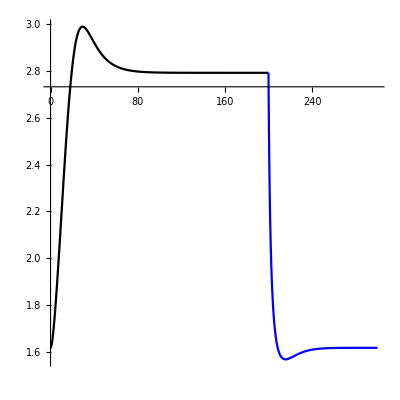
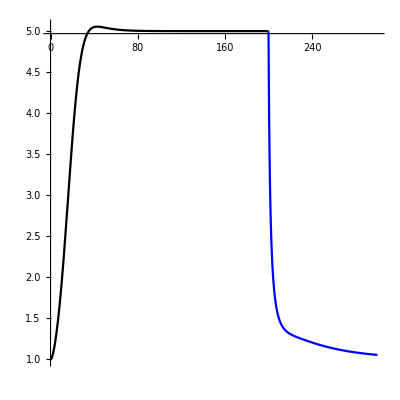
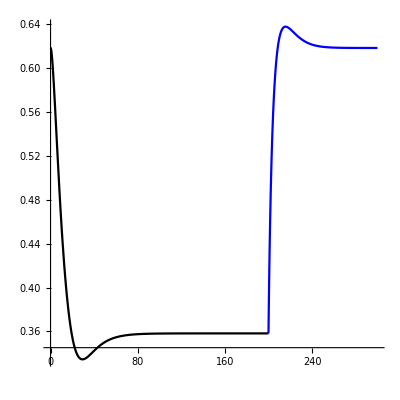
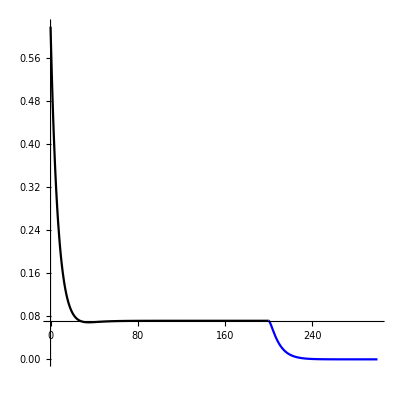
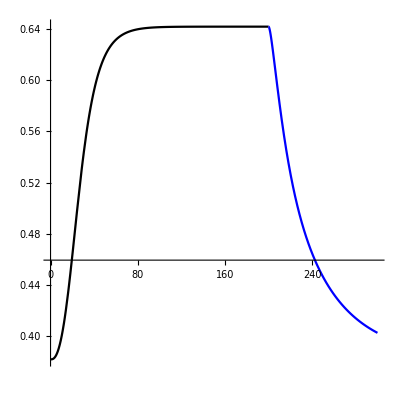
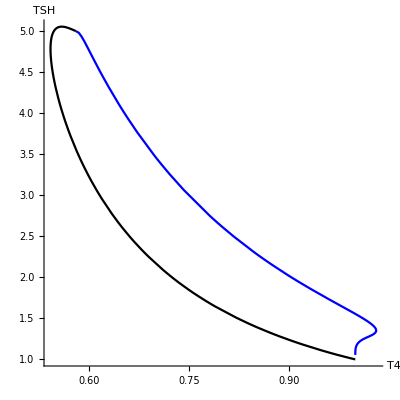
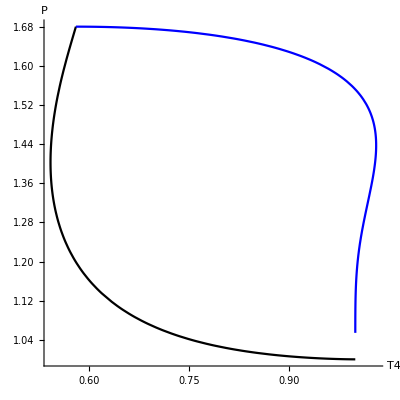

```mathematica
With[{u=1,a1=250.,b1=250.,a2=25.,b2=25.,a3=1/7,b3=1/7,kx2=0,Ab=0,kT=0,at=1/30,bt=1/30,kP=1,ap=1/30,bp=1/30,b30=0,τ=200,tmax=300,atfactor=5 (*thyroid cell killing is enhanced by atfactor (at-> atfactor at *), leg={ "TRH","TSH","T4","T","P"},vars={x1,x2,x3,T,P}},
{(* Computing the normal set point: *)
stst=NSolve[{0==-a1 x1+(b1 u)/x3,0==-a2 x2+(b2 P x1)/x3,0==b3 T ((Ab+x2)/(1+kx2 x2))-a3 x3,0==T (-at+bt (1-kT T) ((Ab+x2)/(1+kx2 x2))),0==P (-ap+(bp (1-kP P))/x3),x1≥0,x2≥0,x3≥0,T≥0,P≥0},vars,Reals][[1]]; 
(* Computing the levothyroxine dosage that will bring the system back to its normal set point (given the disease larger at): *)
rb30 = rightb30/.(NSolve[{0==-a1 x1+(b1 u)/x3,0==-a2 x2+(b2 P x1)/x3,0==rightb30+b3 T ((Ab+x2)/(1+kx2 x2))-a3 x3,0==T (-atfactor at+bt (1-kT T) ((Ab+x2)/(1+kx2 x2))),0==P (-ap+(bp (1-kP P))/x3),x1≥0,x2≥0,rightb30≥0,T≥0,P≥0}/.{x3->(x3/.stst)},{x1,x2,rightb30,T,P},Reals][[1]]);
(* computing the dynamics of the disease: *)
dyn0=Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,atfactor at,bt,kP,ap,bp,x1,x2,x3,T,P]/.stst];
(* Trajectories of the dynamics of the disease + treatment: *)
Table[
Show[{
ParametricPlot[{t,dyn0[[i]]},{t,0,τ},PlotLegends->leg[[i]],PlotStyle->Black],
ParametricPlot[{tt+τ,(Evaluate[dyn[rb30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,atfactor at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[i]])/.t->tt},{tt,0,tmax-τ},PlotStyle->Blue,AspectRatio->1]
},PlotRange->All,AspectRatio->1]
,{i,Range[5]}],
(* Hysteresis fig, T4 vs TSH during disease and treatment: *)
Show[{
ParametricPlot[{dyn0[[3]]/(x3/.stst),dyn0[[2]]/(x2/.stst)},{t,0,τ},PlotStyle->Black],
ParametricPlot[{(Evaluate[dyn[rb30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,atfactor at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[3]])/(x3/.stst)/.t->tt,(Evaluate[dyn[rb30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,atfactor at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[2]])/(x2/.stst)/.t->tt},{tt,0,tmax-τ},PlotStyle->Blue]
},PlotRange->All,AspectRatio->1, AxesLabel-> {"T4","TSH"},AxesOrigin-> {0.4,0}],
(* Hysteresis fig, T4 vs P during disease and treatment: *)
Show[{
ParametricPlot[{dyn0[[3]]/(x3/.stst),dyn0[[5]]/(P/.stst)},{t,0,τ},PlotStyle->Black],
ParametricPlot[{(Evaluate[dyn[rb30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,atfactor at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[3]])/(x3/.stst)/.t->tt,(Evaluate[dyn[rb30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,atfactor at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[5]])/(P/.stst)/.t->tt},{tt,0,tmax-τ},PlotStyle->Blue]
},PlotRange->All,AspectRatio->1,AxesLabel-> {"T4","P"},AxesOrigin-> {0.4,0}]
}
]
```

#### Hysteresis- Fast time scale model - Hashimoto

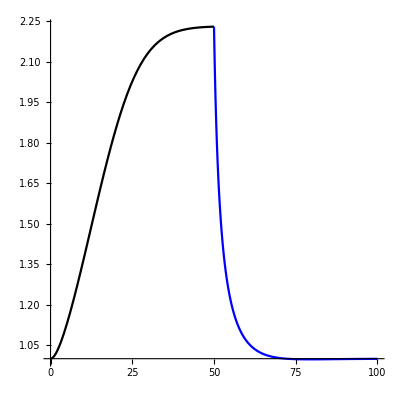
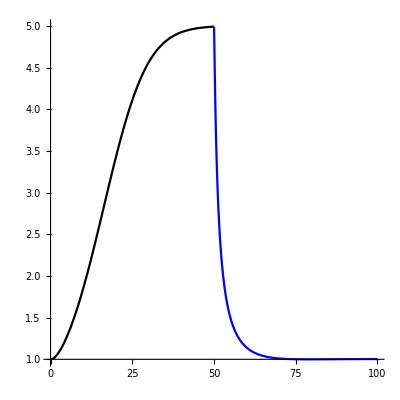
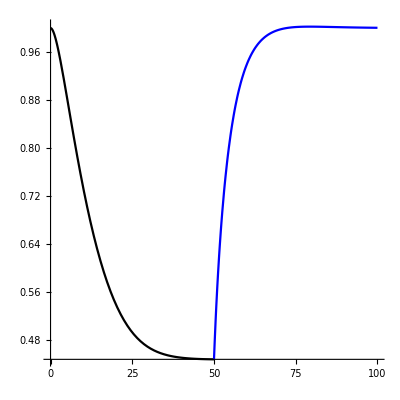
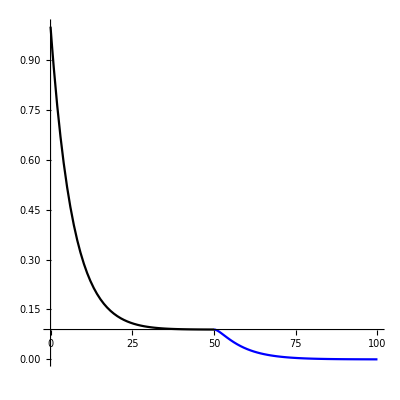
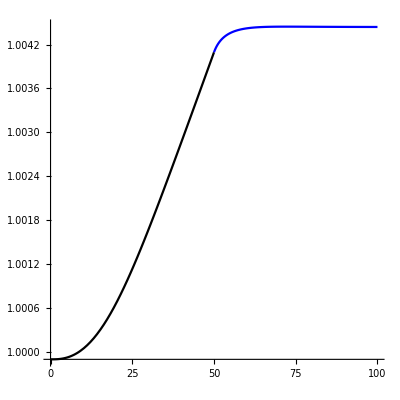
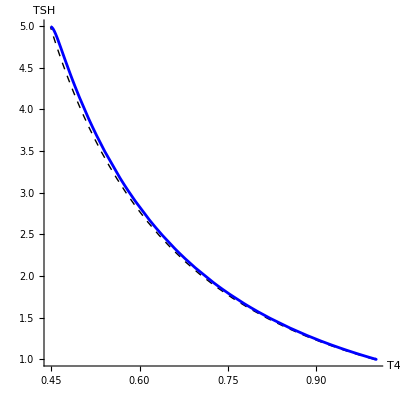
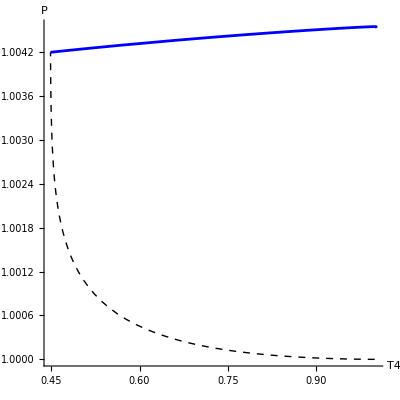

```mathematica
With[{u=1,a1=250.,b1=250.,a2=25.,b2=25.,a3=1/7,b3=1/7,kx2=0,Ab=0,kT=0.0001,at=1/30,bt=1/30,kP=0.0001,ap=1/10000,bp=1/10000,b30=0,τ=50,tmax=100,atfactor=5 (*thyroid cell killing is enhanced by atfactor (at-> atfactor at *), leg={ "TRH","TSH","T4","T","P"},vars={x1,x2,x3,T,P}},
{(* Computing the normal set point: *)
stst=NSolve[{0==-a1 x1+(b1 u)/x3,0==-a2 x2+(b2 P x1)/x3,0==b3 T ((Ab+x2)/(1+kx2 x2))-a3 x3,0==T (-at+bt (1-kT T) ((Ab+x2)/(1+kx2 x2))),0==P (-ap+(bp (1-kP P))/x3),x1≥0,x2≥0,x3≥0,T≥0,P≥0},vars,Reals][[1]]; (* note we only take the first positive solution, but there can be more *)
(* Computing the levothyroxine dosage that will bring the system back to its normal set point (for the disease larger at): *)
rb30 = rightb30/.(NSolve[{0==-a1 x1+(b1 u)/x3,0==-a2 x2+(b2 P x1)/x3,0==rightb30+b3 T ((Ab+x2)/(1+kx2 x2))-a3 x3,0==T (-atfactor at+bt (1-kT T) ((Ab+x2)/(1+kx2 x2))),0==P (-ap+(bp (1-kP P))/x3),x1≥0,x2≥0,rightb30≥0,T≥0,P≥0}/.{x3->(x3/.stst)},{x1,x2,rightb30,T,P},Reals][[1]]);
(* computing the dynamics of the disease: *)
dyn0=Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,atfactor at,bt,kP,ap,bp,x1,x2,x3,T,P]/.stst];
(* Trajectories of the dynamics of the disease + treatment: *)
Table[
Show[{
ParametricPlot[{t,dyn0[[i]]},{t,0,τ},PlotLegends->leg[[i]],PlotStyle->Black],
ParametricPlot[{tt+τ,(Evaluate[dyn[rb30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,atfactor at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[i]])/.t->tt},{tt,0,tmax-τ},PlotStyle->Blue,AspectRatio->1]
},PlotRange->All,AspectRatio->1]
,{i,Range[5]}],
(* Hysteresis fig, T4 vs TSH during disease and treatment: *)
Show[{
ParametricPlot[{dyn0[[3]]/(x3/.stst),dyn0[[2]]/(x2/.stst)},{t,0,τ},PlotStyle->{Black,Dashed,Thick}],
ParametricPlot[{(Evaluate[dyn[rb30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,atfactor at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[3]])/(x3/.stst)/.t->tt,(Evaluate[dyn[rb30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,atfactor at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[2]])/(x2/.stst)/.t->tt},{tt,0,tmax-τ},PlotStyle->{Blue,Thickness[.005]}]
},PlotRange->All,AspectRatio->1, AxesLabel-> {"T4","TSH"},AxesOrigin-> {0.4,0}],
(* Hysteresis fig, T4 vs P during disease and treatment: *)
Show[{
ParametricPlot[{dyn0[[3]]/(x3/.stst),dyn0[[5]]/(P/.stst)},{t,0,τ},PlotStyle->{Black,Dashed,Thick}],
ParametricPlot[{(Evaluate[dyn[rb30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,atfactor at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[3]])/(x3/.stst)/.t->tt,(Evaluate[dyn[rb30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,atfactor at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[5]])/(P/.stst)/.t->tt},{tt,0,tmax-τ},PlotStyle->{Blue,Thickness[.005]}]
},PlotRange->All,AspectRatio->1,AxesLabel-> {"T4","P"},AxesOrigin-> {0.4,0}]
}
]
```

#### Hysteresis - Graves’

```mathematica
stst=.
```

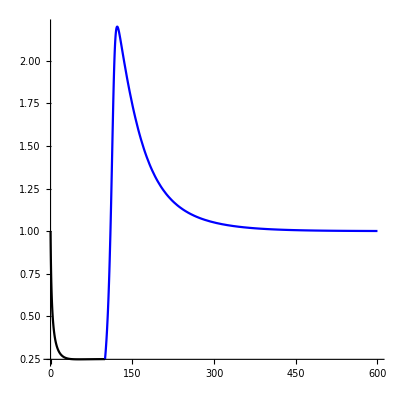
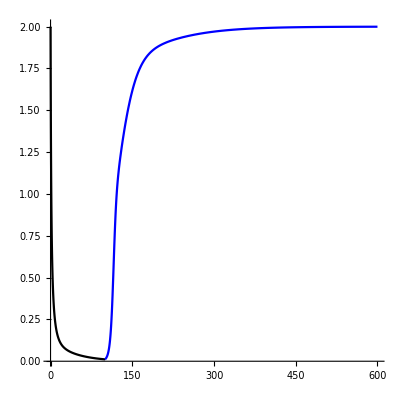
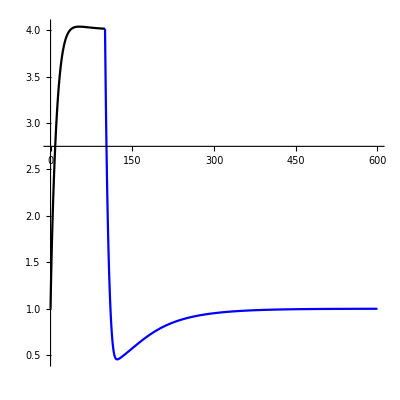
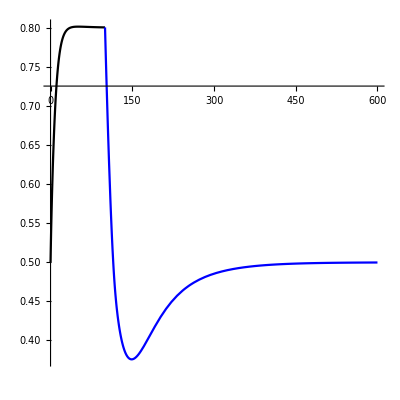
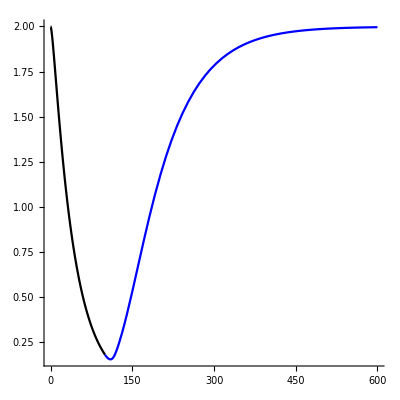
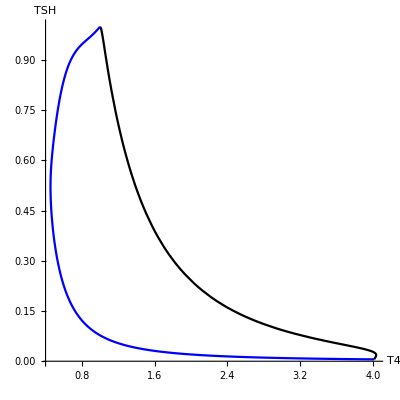
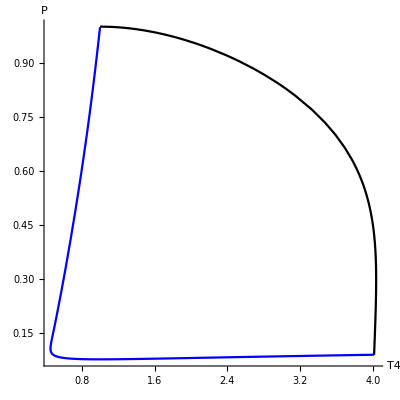

```mathematica
With[{u=1,a1=250.,b1=250.,a2=25.,b2=25.,a3=1/7,b3=1/7,kx2=0,Ab=5,kT=1,at=1/30,bt=1/30,kP=0.0001,ap=1/30,bp=1/30,b30=0,Abdrug=0 (*antibody levels under the influence of antithyroid drug treatment*),τ=100,tmax=600, leg={ "TRH","TSH","T4","T","P"},vars={x1,x2,x3,T,P}},
{(* Computing the normal set point: *)
stst=NSolve[{0==-a1 x1+(b1 u)/x3,0==-a2 x2+(b2 P x1)/x3,0==b3 T (x2/(1+kx2 x2))-a3 x3,0==T (-at+bt (1-kT T) (x2/(1+kx2 x2))),0==P (-ap+(bp (1-kP P))/x3),x1≥0,x2≥0,x3≥0,T≥0,P≥0},vars,Reals][[1]]; (* note we only take the first positive solution, but there can be more *)
(* Computing the antithyroid drug dosage that will bring the system back to its normal set point (given the disease Ab): *)
b3drug = rightb3/.(NSolve[{0==-a1 x1+(b1 u)/x3,0==-a2 x2+(b2 P x1)/x3,0==rightb3 T ((Abdrug+x2)/(1+kx2 x2))-a3 x3,0==T (- at+bt (1-kT T) ((Abdrug+x2)/(1+kx2 x2))),0==P (-ap+(bp (1-kP P))/x3),x1≥0,x2≥0,rightb3≥0,T≥0,P≥0}/.{x3->(x3/.stst)},{x1,x2,rightb3,T,P},Reals][[1]]);
(* computing the dynamics of the disease: *)
dyn0=Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT, at,bt,kP,ap,bp,x1,x2,x3,T,P]/.stst];
(* Trajectories of the dynamics of the disease + treatment: *)
Table[
Show[{
ParametricPlot[{t,dyn0[[i]]},{t,0,τ},PlotLegends->leg[[i]],PlotStyle->Black],
ParametricPlot[{tt+τ,(Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,b3drug,kx2,Abdrug,kT, at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[i]])/.t->tt},{tt,0,tmax-τ},PlotStyle->Blue,AspectRatio->1]
},PlotRange->All,AspectRatio->1]
,{i,Range[5]}],
(* Hysteresis fig, T4 vs TSH during disease and treatment: *)
Show[{
ParametricPlot[{dyn0[[3]]/(x3/.stst),dyn0[[2]]/(x2/.stst)},{t,0,τ},PlotStyle->Black],
ParametricPlot[{(Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,b3drug,kx2,Abdrug,kT, at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[3]])/(x3/.stst)/.t->tt,(Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,b3drug,kx2,Abdrug,kT, at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[2]])/(x2/.stst)/.t->tt},{tt,0,tmax-τ},PlotStyle->Blue]
},PlotRange->All,AspectRatio->1, AxesLabel-> {"T4","TSH"},AxesOrigin-> {0.4,0}],
(* Hysteresis fig, T4 vs P during disease and treatment: *)
Show[{
ParametricPlot[{dyn0[[3]]/(x3/.stst),dyn0[[5]]/(P/.stst)},{t,0,τ},PlotStyle->Black],
ParametricPlot[{(Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,b3drug,kx2,Abdrug,kT, at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[3]])/(x3/.stst)/.t->tt,(Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,b3drug,kx2,Abdrug,kT, at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[5]])/(P/.stst)/.t->tt},{tt,0,tmax-τ},PlotStyle->Blue]
},PlotRange->All,AspectRatio->1,AxesLabel-> {"T4","P"},AxesOrigin-> {0.4,0}]
}
]
```

#### Hysteresis - Graves’ - Fast time scale model

```mathematica
stst=.
```

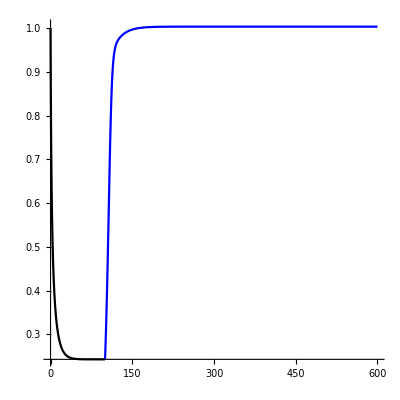
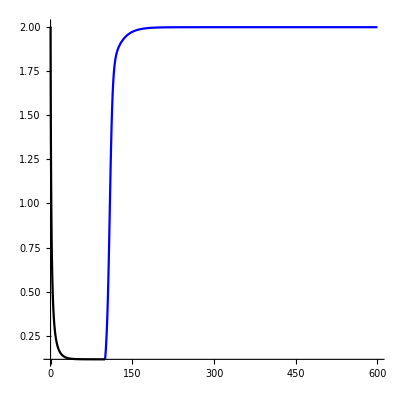
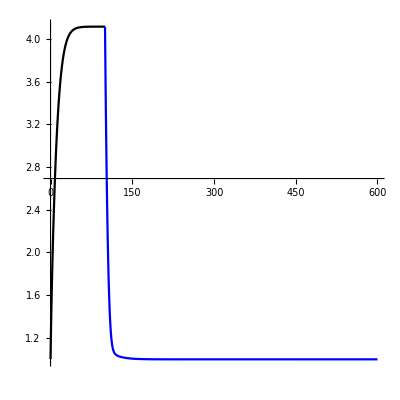
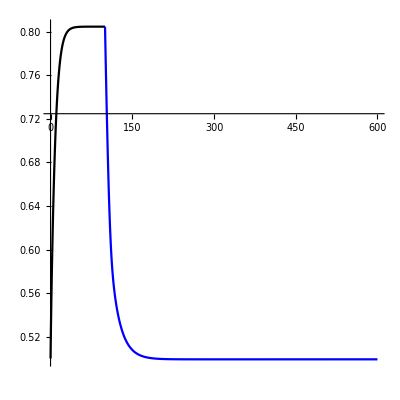
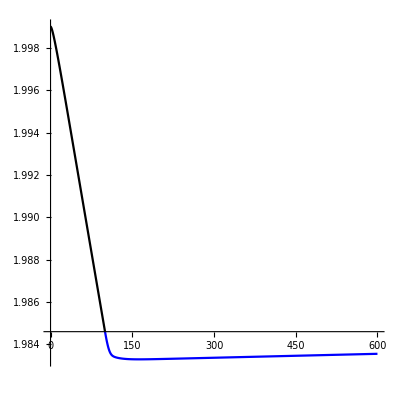
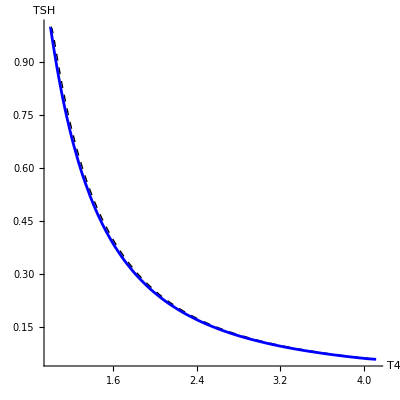
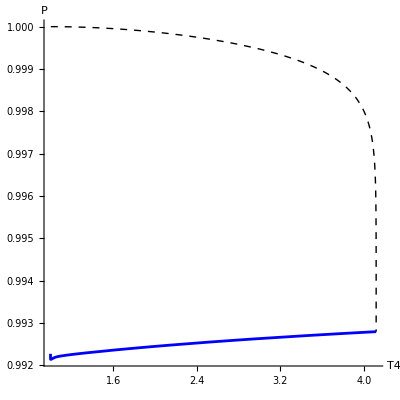

```mathematica
With[{u=1,a1=250.,b1=250.,a2=25.,b2=25.,a3=1/7,b3=1/7,kx2=0,Ab=5,kT=1,at=1/30,bt=1/30,kP=0.0001,ap=1/10000,bp=1/10000,b30=0,Abdrug=0,(*b3drug=0.05,*)τ=100,tmax=600, leg={ "TRH","TSH","T4","T","P"},vars={x1,x2,x3,T,P}},
{(* Computing the normal set point: *)
stst=NSolve[{0==-a1 x1+(b1 u)/x3,0==-a2 x2+(b2 P x1)/x3,0==b3 T (x2/(1+kx2 x2))-a3 x3,0==T (-at+bt (1-kT T) (x2/(1+kx2 x2))),0==P (-ap+(bp (1-kP P))/x3),x1≥0,x2≥0,x3≥0,T≥0,P≥0},vars,Reals][[1]]; (* note we only take the first positive solution, but there can be more *)
(* Computing the levothyroxine dosage that will bring the system back to its normal set point (for the disease larger at): *)
b3drug = rightb3/.(NSolve[{0==-a1 x1+(b1 u)/x3,0==-a2 x2+(b2 P x1)/x3,0==rightb3 T ((Abdrug+x2)/(1+kx2 x2))-a3 x3,0==T (- at+bt (1-kT T) ((Abdrug+x2)/(1+kx2 x2))),0==P (-ap+(bp (1-kP P))/x3),x1≥0,x2≥0,rightb3≥0,T≥0,P≥0}/.{x3->(x3/.stst)},{x1,x2,rightb3,T,P},Reals][[1]]);
(* computing the dynamics of the disease: *)
dyn0=Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT, at,bt,kP,ap,bp,x1,x2,x3,T,P]/.stst];
(* Trajectories of the dynamics of the disease + treatment: *)
Table[
Show[{
ParametricPlot[{t,dyn0[[i]]},{t,0,τ},PlotLegends->leg[[i]],PlotStyle->Black],
ParametricPlot[{tt+τ,(Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,b3drug,kx2,Abdrug,kT, at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[i]])/.t->tt},{tt,0,tmax-τ},PlotStyle->Blue,AspectRatio->1]
},PlotRange->All,AspectRatio->1]
,{i,Range[5]}],
(* Hysteresis fig, T4 vs TSH during disease and treatment: *)
Show[{
ParametricPlot[{dyn0[[3]]/(x3/.stst),dyn0[[2]]/(x2/.stst)},{t,0,τ},PlotStyle->{Black,Dashed,Thick}],
ParametricPlot[{(Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,b3drug,kx2,Abdrug,kT, at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[3]])/(x3/.stst)/.t->tt,(Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,b3drug,kx2,Abdrug,kT, at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[2]])/(x2/.stst)/.t->tt},{tt,0,tmax-τ},PlotStyle->{Blue,Thickness[.005]}]
},PlotRange->All,AspectRatio->1, AxesLabel-> {"T4","TSH"},AxesOrigin-> {0.4,0}],
(* Hysteresis fig, T4 vs P during disease and treatment: *)
Show[{
ParametricPlot[{dyn0[[3]]/(x3/.stst),dyn0[[5]]/(P/.stst)},{t,0,τ},PlotStyle->{Black,Dashed,Thick}],
ParametricPlot[{(Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,b3drug,kx2,Abdrug,kT, at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[3]])/(x3/.stst)/.t->tt,(Evaluate[dyn[b30,u,a1,b1,a2,b2,a3,b3drug,kx2,Abdrug,kT, at,bt,kP,ap,bp,#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]&@(dyn0/.t->τ)][[5]])/(P/.stst)/.t->tt},{tt,0,tmax-τ},PlotStyle->{Blue,Thickness[.005]}]
},PlotRange->All,AspectRatio->1,AxesLabel-> {"T4","P"},AxesOrigin-> {0.4,0}]
}
]
```

## Nullcline analysis

### Computation of null clines

```mathematica
eq = {x1'[t]==-a1 x1[t]+(b1 u)/x3[t],
x2'[t]==-a2 x2[t]+(b2 P[t] x1[t])/x3[t],
x3'[t]==b30+(b3 T[t] (Ab+x2[t]))/(1+kx2 (Ab+x2[t]))-a3 x3[t],
T'[t]==T[t] (-at+(bt (1-kT T[t]) (Ab+x2[t]))/(1+kx2 (Ab+x2[t]))),
P'[t]==P[t] (-ap+(bp (1-kP P[t]))/x3[t])}
```

{x1'[t]==-a1 x1[t]+(b1 u)/x3[t],x2'[t]==-a2 x2[t]+(b2 P[t] x1[t])/x3[t],x3'[t]==b30+(b3 T[t] (Ab+x2[t]))/(1+kx2 (Ab+x2[t]))-a3 x3[t],T'[t]==T[t] (-at+(bt (1-kT T[t]) (Ab+x2[t]))/(1+kx2 (Ab+x2[t]))),P'[t]==P[t] (-ap+(bp (1-kP P[t]))/x3[t])}

For the sake of clarity we start with a scaling of the variables by  their steady  state values of the simple model  (i.e. Ab=kx2=b30=0)  and with inifnite carrying capacity (i.e. kT=kP=0):

```mathematica
#[[1]]->#[[2]]#[[1]]&/@Solve[eq/.kP|kT|b30|Ab|kx2|x_'[t]->0,{x1[t],x2[t],x3[t],P[t],T[t]}][[1]]
D[#[[1]],t]->#[[2]]D[#[[1]],t]&/@Solve[eq/.kP|kT|b30|Ab|kx2|x_'[t]->0,{x1[t],x2[t],x3[t],P[t],T[t]}][[1]]
```

```mathematica
{x1[t]->(ap b1 u)/(a1 bp)x1[t],x2[t]->at/bt x2[t],x3[t]->bp/ap x3[t],P[t]->(a1 a2 at bp^2)/(ap^2 b1 b2 bt u)P[t],T[t]->(a3 bp bt)/(ap at b3)T[t]}
```

```mathematica
{x1'[t]->(ap b1 u)/(a1 bp)x1'[t],x2'[t]->at/bt x2'[t],x3'[t]->bp/ap x3'[t],P'[t]->(a1 a2 at bp^2)/(ap^2 b1 b2 bt u)P'[t],T'[t]->(a3 bp bt)/(ap at b3)T'[t]}
```

With this and the redefinition of the parameters :
	Ab->at/bt AB
	kx2 ->  bt/atKX2
	kT-> (ap at b3)/(a3 bp bt)KT
	kP->(ap^2 b1 b2 bt)/(a1 a2 at bp^2)KP
	b30->(a3 bp)/apB30
the model equations transform to:

```mathematica
seq={1/a1 x1'[t]==1/x3[t]-x1[t],
1/a2 x2'[t]==P[t] x1[t]/x3[t]-x2[t],
1/a3 x3'[t]==B30+(T[t](AB+ x2[t])/(1+KX2(AB+x2[t]))-x3[t]),
1/at T'[t]==T[t] ((AB+x2[t])/(1+KX2(AB+ x2[t]))(1-KT T[t])-1),
1/ap P'[t]==P[t](1/x3[t](1-KP P[t])-1)};
```

Note that with the choice AB=KX2=B30=KP=KT=0 we recover the simple model.

To compute the nullclines dT/dt=0, dP/dt=0 we use the separation of time scales - the hormone turnover times are much faster than the gland turnover times. We separate the model to the hormone “fast” equations:

```mathematica
{1/a1 x1'[t]==1/x3[t]-x1[t],
1/a2 x2'[t]==P[t] x1[t]/x3[t]-x2[t],
1/a3 x3'[t]==B30+(T[t](AB+ x2[t])/(1+KX2(AB+x2[t]))-x3[t])}
```

and the gland “slow” equations:

```mathematica
{1/at T'[t]==T[t] ((AB+x2[t])/(1+KX2(AB+ x2[t]))(1-KT T[t])-1),
1/ap P'[t]==P[t](1/x3[t](1-KP P[t])-1)}
```

We  first solve the steady-states for the hormone equations. The solution as a function of P and T can be represented as the roots of a third degree polynomial. For the sake of clarity we express x1 and x3 using x2, and write an implicit equation for x2.

```mathematica
TableForm[Solve[{0==1/x3[t]-x1[t],0==P[t] x1[t]/x3[t]-x2[t]},{x1[t],x3[t]}][[2]]]
```

x1[t]→(√x2[t])/(√P[t])
x3[t]→(√P[t])/(√x2[t])

```mathematica
B30+(T[t](AB+x2[t])/(1+KX2(AB+x2[t]))- √(P[t]/x2[t]))==0
```

With this, the “slow time scale” system is composed of two ODE’s for  P and T and one implicit algebraic equation for x2:

```mathematica
{1/at T'[t]==T[t] ((AB+x2[t])/(1+KX2(AB+ x2[t]))(1-KT T[t])-1),
1/ap P'[t]==P[t](√(x2[t]/P[t])(1-KP P[t])-1),
B30+(T[t](AB+x2[t])/(1+KX2(AB+x2[t]))- √(P[t]/x2[t]))==0}
```

In order to find the nullclines we need to solve the equations dT/dt=0 and dP/dt=0.  One trivial solution is T=0, P=0. 
In order to find this non trivial solution we can eliminate x2 from each equation (In a nutshell, the equations T’=0 and P’=0 can be solved each for x2. Then, the solution can be substituted into the implicit equation for x2):

```mathematica
({1/at T'==T ((AB+x2)/(1+KX2(AB+ x2))(1-KT T)-1),
1/ap P'==P(√(x2/P)(1-KP P)-1)}/.x_'->0/.{x1->(√x2)/(√P),x3->(√P)/(√x2)})
```

{0==T (-1+((1-KT T) (AB+x2))/(1+KX2 (AB+x2))),0==P (-1+(1-KP P) √(x2/P))}

```mathematica
B30+(T[t](AB+x2[t])/(1+KX2(AB+x2[t]))- √(P[t]/x2[t]))==0/.Solve[#,x2[t]][[1]]&/@{(AB+x2[t])/(1+KX2(AB+ x2[t]))(1-KT T[t])-1==0,√(x2[t]/P[t])(1-KP P[t])-1==0}/.x_[t]->x//FullSimplify//Quiet
```

{T/(-1+KT T)+√(-(P (-1+KX2+KT T))/(1+AB (-1+KX2+KT T)))==B30,B30+((AB+P/(-1+KP P)^2) T)/(1+AB KX2+(KX2 P)/(-1+KP P)^2)==√((-1+KP P)^2)}

```mathematica
FullSimplify@PowerExpand@FullSimplify@Solve[T/(-1+KT T)+√(-(P (-1+KX2+KT T))/(1+AB (-1+KX2+KT T)))==B30,P]
```

{{P→-((B30+T-B30 KT T)^2 (1+AB (-1+KX2+KT T)))/((-1+KT T)^2 (-1+KX2+KT T))}}

```mathematica
P->(T+B30(1-KT T))^2/(1-KT T)^2(1/(1-KX2-KT T)-AB )
```

```mathematica
FullSimplify@PowerExpand@FullSimplify@Solve[B30+((AB+P/(-1+KP P)^2) T)/(1+AB KX2+(KX2 P)/(-1+KP P)^2)==-(KP P-1),T]
```

{{T→((1-B30-KP P) (1+AB KX2+(KX2 P)/(-1+KP P)^2))/(AB+P/(-1+KP P)^2)}}

```mathematica
FullSimplify@PowerExpand[{{P->(T+B30(1-KT T))^2/(1-KT T)^2(1/(1-KX2-KT T)-AB )},{T->(1-B30-KP P)(1+AB KX2(1+P/(1-KP P)^2))/(AB+P/(1-KP P)^2)}}/.{B30-> 0,AB->0,KX2->0}]
```

{{P→T^2/(1-KT T)^3},{T→(1-KP P)^3/P}}

Therefore, the null clines are:
T’=0:  P=(T+B30(1-KT T))^2/(1-KT T)^2(1/(1-KX2-KT T)-AB )  or  T=0
P’=0:  T=((1-B30-KP P) (1+AB KX2+(KX2 P)/(-1+KP P)^2))/(AB+P/(-1+KP P)^2)  or  P=0

The nullclines in the simple case, i.e. B30=AB=KX2=0, takes the simple form of: 
T’=0:  P=T^2/(1-KT T)^3  or  T=0
P’=0:  T→(1-KP P)^3/P  or  P=0

```mathematica
Manipulate[
Show[ContourPlot[
{P== -((B30+T-B30 KT T)^2 (1+AB (-1+KX2+KT T)))/((-1+KT T)^2 (-1+KX2+KT T)),T==((1-B30-KP P) (1+AB KX2+(KX2 P)/(-1+KP P)^2))/(AB+P/(-1+KP P)^2)},
{T,0,Tmax},{P,0,Pmax},PlotRange->{{0,Tmax},{0,Pmax}},PerformanceGoal->"Quality",PlotLegends->Placed[{"T'=0","P'=0"},Below],ContourStyle->{Orange,Blue}],
ParametricPlot[{0,P},{P,0,Pmax},PlotStyle->Orange],ParametricPlot[{T,0},{T,0,Tmax},PlotStyle->Blue]],
{KT,1,1},{KP,1,1},{AB,0,2},{B30,0,1},{KX2,0,1},{Pmax,1},{Tmax,1}]
```

## stability analysis

In order to validate the stability of the slow system we need to find the signs of the eigenvalues of the Jacobian of the reduced system (P,T) at the steady state. 
The system has three fixed points: (i) One at T>0, P>0,  (ii) another one at T>0, P=0, and (iii) a third one at T=0, P=0. (iiii) T=0, P>0
(i) We first inspect the solution at T>0, P>0.
 To calculate the stability of this fixed point we need to calculate the partial derivative of x2 with respect to P and T

```mathematica
TableForm[dx2=Solve[
D[0==B30-√(P/x2[P,T])+(T (AB+x2[P,T]))/(1+KX2 (AB+x2[P,T])),{{P,T}}],{Derivative[1,0][x2][P,T],Derivative[0,1][x2][P,T]}][[1]]/.x2[__]->x2//FullSimplify//PowerExpand//FullSimplify]
```

x2^(1,0)[P,T]→1/(P/x2+(2 √P T √x2)/(1+KX2 (AB+x2))^2)
x2^(0,1)[P,T]→-(2 x2^(3/2) (AB+x2) (1+KX2 (AB+x2)))/(2 T x2^(3/2)+√P (1+KX2 (AB+x2))^2)

Calculating the Jacobian and substituting the above we find:

```mathematica
MatrixForm[JTP=D[{at T (-1+((1-KT T) (AB+x2[P,T]))/(1+KX2 (AB+x2[P,T]))),ap P (-1+(1-KP P) √(x2[P,T]/P))},{{T,P}}]/.dx2/.x2[__]->x2//PowerExpand//FullSimplify]
```

(at (-1+((1-KT T) (AB+x2))/(1+KX2 (AB+x2))-(T (AB+x2) (2 x2^(3/2)+KT √P (1+KX2 (AB+x2))^2))/((1+KX2 (AB+x2)) (2 T x2^(3/2)+√P (1+KX2 (AB+x2))^2))) | -(at T (-1+KT T) x2)/(2 √P T x2^(3/2)+P (1+KX2 (AB+x2))^2)
(ap √P (-1+KP P) x2 (AB+x2) (1+KX2 (AB+x2)))/(2 T x2^(3/2)+√P (1+KX2 (AB+x2))^2) | ap (-1-KP √P √x2+((1-KP P) √x2)/(√P)+((-1+KP P) T x2^2)/(2 √P T x2^(3/2)+P (1+KX2 (AB+x2))^2)))

Since it is hard to find the steady state solution of P,T and x2,  the best next thing is to find a simple expression which connects the steady state solution of P, T and x2 in this system:

```mathematica
{((1-KT T) (AB+x2))/(1+KX2 (AB+x2))==1, (1-KP P) √(x2/P)==1}
```

Note that from this we learn that for a non-negative solution to exist (1-KT T)>0 and (1-KP P)>0.  Substituting this into the Jacobian we find

```mathematica
MatrixForm[jtp=JTP/.{(AB+x2)/(1+KX2 (AB+x2))(1-KT T)->1,(√x2)/(√P)(1-KP P)->1}//FullSimplify//PowerExpand//FullSimplify]
```

```mathematica
({{-(at T (AB+x2) (2 x2^(3/2)+KT √P (1+KX2 (AB+x2))^2))/((1+KX2 (AB+x2)) (2 T x2^(3/2)+√P (1+KX2 (AB+x2))^2)), -(at T (-1+KT T) x2)/(2 √P T x2^(3/2)+P (1+KX2 (AB+x2))^2)}, {(ap √P (-1+KP P) x2 (AB+x2) (1+KX2 (AB+x2)))/(2 T x2^(3/2)+√P (1+KX2 (AB+x2))^2), ap (-KP √P √x2+((-1+KP P) T x2^2)/(2 √P T x2^(3/2)+P (1+KX2 (AB+x2))^2))}})
```

For this steady state solution to be stable the eigenvalues must all have negative real part. A necessary and sufficient condition for this in 2D systems is that the trace is negative and the determinant is positive. A quick look at J shows that this is indeed the case.

```mathematica
Refine[
FullSimplify[
Tr[jtp]<0&&x2>0&&P>0&&T>0&&KP>0&&KT>0&&AB>0&&a>0&&KX2>0&&KP P<1],x2>0&&P>0&&T>0&&KP>0&&KT>0&&AB>0&&a>0&&KX2>0&&KP P<1]
```

True

```mathematica
Refine[
FullSimplify[
Det[jtp]>0&&x2>0&&P>0&&T>0&&KP>0&&KT>0&&AB>0&&a>0&&KX2>0&&KP P<1],x2>0&&P>0&&T>0&&KP>0&&KT>0&&AB>0&&a>0&&KX2>0&&KP P<1]
```

True

Therefore, when this fixed point exists it is stable.

(ii) We next inspect the stability of the second fixed point at P=0, T>0. This fixed point can be computed explicitly: {x1=(KT (1+AB KX2))/(-1+AB+B30 KT-AB KX2+AB B30 KT KX2),x2=0,x3=(-1+AB+B30 KT-AB KX2+AB B30 KT KX2)/(KT (1+AB KX2)),P=0,T=(-1+AB-AB KX2)/(AB KT)}:

```mathematica
PowerExpand@Solve[#==0&/@{1/x3[t]-x1[t],
x2[t],
B30+(T[t](AB+ x2[t])/(1+KX2(AB+x2[t]))-x3[t]),
T[t] ((AB+x2[t])/(1+KX2(AB+ x2[t]))(1-KT T[t])-1),
 P[t]}/.x_[t]->x,{x1,x2,x3,P,T}]
```

{{x1→(KT (1+AB KX2))/(-1+AB+B30 KT-AB KX2+AB B30 KT KX2),x2→0,x3→(-1+AB+B30 KT-AB KX2+AB B30 KT KX2)/(KT (1+AB KX2)),P→0,T→(-1+AB-AB KX2)/(AB KT)},{x1→1/B30,x2→0,x3→B30,P→0,T→0}}

This fixed point is positive only if AB>1/(1-KX2):

```mathematica
Reduce[-1+AB+B30 KT-AB KX2+AB B30 KT KX2>0&&-1+AB-AB KX2>0&&KT>0&&ap>0&&AB>0&&B30>0&&KX2>0]
```

ap>0&&KT>0&&0<KX2<1&&AB>-1/(-1+KX2)&&B30>0

If KX2=0 this condition is reduced to AB>1.
The eigenvalues of the Jacobian at this fixed point are: {-1,-1,-1,at+AB at (-1+2 KX2),(ap (1+KT-B30 KT+AB (-1+(1+KT-B30 KT) KX2)))/(-1+AB+B30 KT+AB (-1+B30 KT) KX2)}:

```mathematica
FullSimplify[D[{-x1+1/x3,-x2+(P x1)/x3,T (AB+x2)-x3,at T (-1+(1-KT T) (AB+x2)),ap P (-1+(1-KP P)/x3)},{{x1,x2,x3,T,P}}]/.{{x1->(KT (1+AB KX2))/(-1+AB+B30 KT-AB KX2+AB B30 KT KX2),x2->0,x3->(-1+AB+B30 KT-AB KX2+AB B30 KT KX2)/(KT (1+AB KX2)),P->0,T->(-1+AB-AB KX2)/(AB KT)}}//FullSimplify//Eigenvalues]
```

{-1,-1,-1,at+AB at (-1+2 KX2),(ap (1+KT-B30 KT+AB (-1+(1+KT-B30 KT) KX2)))/(-1+AB+B30 KT+AB (-1+B30 KT) KX2)}

The eigenvalues are negative providing that AB>(1+KT-B30 KT)/(1-KX2-KT KX2+B30 KT KX2).

```mathematica
Reduce[(1-AB+2 AB KX2)<0&&-(ap (-1+AB-KT+B30 KT-AB KX2-AB KT KX2+AB B30 KT KX2))/(-1+AB+B30 KT-AB KX2+AB B30 KT KX2)<0&&KT>0&&ap>0&&AB>0&&B30>0&&KX2>0]
```

0<KX2<1/2&&AB>-1/(-1+2 KX2)&&((0<B30<1&&0<KT<(1-AB+AB KX2)/(-1+B30-AB KX2+AB B30 KX2)&&ap>0)||(B30≥1&&KT>0&&ap>0))

```mathematica
Solve[KT==(1-AB+AB KX2)/(-1+B30-AB KX2+AB B30 KX2),AB]
```

{{AB→(1+KT-B30 KT)/(1-KX2-KT KX2+B30 KT KX2)}}

In the simple case when there is no external thyroid hormone supply B30=0, and KX2=0, this condition is reduced to AB>1+KT.

(iii) We inspect the stability of the third fixed point at P=0, T=0. This fixed point can be computed explicitly (see above): {x1=1/B30,x2=0,x3=B30,P=0,T=0}. Note that this fixed point exists only if there is an external thyroid hormone supply B30>0. 
In this case, the eigenvalues of the Jacobian are {ap (-1+1/B30),-1,-1,-1,(-1+AB) at}:

```mathematica
FullSimplify[D[{-x1+1/x3,-x2+(P x1)/x3,T (AB+x2)-x3,at T (-1+(1-KT T) (AB+x2)),ap P (-1+(1-KP P)/x3)},{{x1,x2,x3,T,P}}]/.{{x1->1/B30,x2->0,x3->B30,P->0,T->0}}//FullSimplify//Eigenvalues]
```

{ap (-1+1/B30),-1,-1,-1,(-1+AB) at}

The eigenvalues are negative providing that AB<1 and B30>1.

```mathematica
Reduce[(-1+1/B30)<0&&-1+AB<0&&KT>0&&ap>0&&AB>0&&B30>0&&KX2>0]
```

KT>0&&ap>0&&0<AB<1&&B30>1&&KX2>0

(iiii) Finally, we inspect the stabiliy of the fourth fixed point at T=0, P>0. This point can be computed explicitly: {x1=1/B30,x2=(1-B30)/(B30^2 KP),x3=B30,P=(1-B30)/KP,T=0}

```mathematica
PowerExpand@Solve[#==0&/@{1/x3[t]-x1[t],
P[t] x1[t]/x3[t]-x2[t],
B30-x3[t],
T[t],
 P[t](1/x3[t](1-KP P[t])-1)}/.x_[t]->x,{x1,x2,x3,P,T}]
```

{{x1→1/B30,x2→0,x3→B30,P→0,T→0},{x1→1/B30,x2→(1-B30)/(B30^2 KP),x3→B30,P→(1-B30)/KP,T→0}}

This fixed point is positive only if B30<1.
In this case, the eigenvalues of the Jacobian are {(ap (-1+B30))/B30,-1,-1,-1,at (-1+AB+(1-B30)/(B30^2 KP))}:

```mathematica
FullSimplify[D[{-x1+1/x3,-x2+(P x1)/x3,T (AB+x2)-x3,at T (-1+(1-KT T) (AB+x2)),ap P (-1+(1-KP P)/x3)},{{x1,x2,x3,T,P}}]/.{{x1->1/B30,x2->(1-B30)/(B30^2 KP),x3->B30,P->(1-B30)/KP,T->0}}//FullSimplify//Eigenvalues]
```

{(ap (-1+B30))/B30,-1,-1,-1,at (-1+AB+(1-B30)/(B30^2 KP))}

The eigenvalues are negative providing that B30>1 and AB<1-(1-B30)/(B30^2 KP).

```mathematica
Manipulate[
Show[ContourPlot[
{P== -((B30+T-B30 KT T)^2 (1+AB (-1+KX2+KT T)))/((-1+KT T)^2 (-1+KX2+KT T)),T==((1-B30-KP P) (1+AB KX2+(KX2 P)/(-1+KP P)^2))/(AB+P/(-1+KP P)^2)}
,
{T,0,Tmax},{P,0,Pmax},PlotRange->{{0,Tmax},{0,Pmax}},PerformanceGoal->"Quality",PlotLegends->Placed[{"T'=0","P'=0"},Below],ContourStyle->{Orange,Blue}],
ParametricPlot[{0,P},{P,0,Pmax},PlotStyle->Orange],ParametricPlot[{T,0},{T,0,Tmax},PlotStyle->Blue],
StreamPlot[{},{T,0,Tmax},{P,0,Pmax}]],
{KT,1,1},{KP,1,1},{AB,0,2},{B30,0,1},{KX2,0,1},{Pmax,1},{Tmax,1}]
```

### Nullclines and stream plots for the different parameter regimes

Equations:

```mathematica
eq={at T[t] ((AB+x2[t])/(1+KX2(AB+ x2[t]))(1-KT T[t])-1),ap P[t](√(x2[t]/P[t])(1-KP P[t])-1),B30+(T[t](AB+x2[t])/(1+KX2(AB+x2[t]))- √(P[t]/x2[t]))==0};
```

Parameter sets:

simple set
KX2=AB=KT=KP=B30=0

```mathematica
gradSimple=Most@#/.Solve[#[[-1]],x2][[1]]&@(eq/.KX2|B30|AB|KT|KP->0/.x_[t]->x/.at|ap->1)
```

{(-1+P^(1/3)/T^(2/3)) T,P (-1+√(1/(P^(2/3) T^(2/3))))}

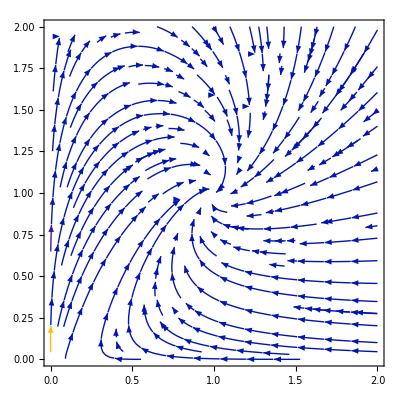

```mathematica
StreamPlot[gradSimple,{T,0,2},{P,0,2},PlotRangePadding->None]
```

CC set
KX2=AB=B30=0, KT=KP=1

```mathematica
gradCC=Most@#/.Solve[#[[-1]],x2][[1]]&@(eq/.KX2|B30|AB->0/.KT|KP->1/.x_[t]->x/.at|ap->1)
```

{(-1+(P^(1/3) (1-T))/T^(2/3)) T,P (-1+(1-P) √(1/(P^(2/3) T^(2/3))))}

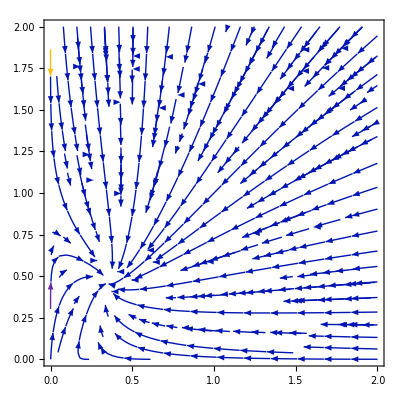

```mathematica
StreamPlot[gradCC,{T,0,2},{P,0,2},PlotRangePadding->None]
```

Weak Graves
KX2=B30=0, KT=KP=1, AB<1
we expect one stable point at T>0,P>0

```mathematica
gradGraves=Most@#/.Solve[#[[-1]],x2][[1]]&@(eq/.KX2|B30->0/.KT|KP->1/.x_[t]->x/.at|ap->1)//Quiet
```

{T (-1+(1-T) (AB+1/3 (-2 AB+(2^(1/3) AB^2 T^2)/((27 P T^4+2 AB^3 T^6+3 √3 √(27 P^2 T^8+4 AB^3 P T^10))^(1/3))+((27 P T^4+2 AB^3 T^6+3 √3 √(27 P^2 T^8+4 AB^3 P T^10))^(1/3))/(2^(1/3) T^2)))),P (-1+((1-P) √((-2 AB+(2^(1/3) AB^2 T^2)/((27 P T^4+2 AB^3 T^6+3 √3 √(27 P^2 T^8+4 AB^3 P T^10))^(1/3))+((27 P T^4+2 AB^3 T^6+3 √3 √(27 P^2 T^8+4 AB^3 P T^10))^(1/3))/(2^(1/3) T^2))/P))/(√3))}

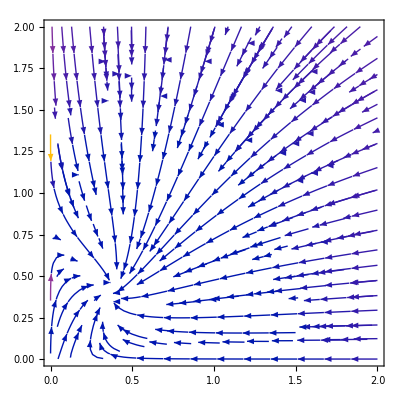

```mathematica
StreamPlot[Evaluate[gradGraves/.AB->0.5],{T,0,2},{P,0,2},PlotRangePadding->None]
```

Medium Graves
KX2=B30=0, KT=KP=1, 1<AB<2
we expect one stable point at T>0,P>0 and another unstable point at P=0, T>0

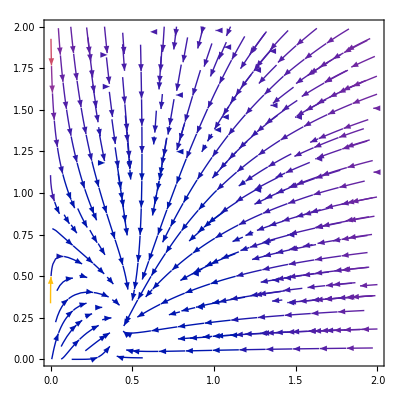

```mathematica
StreamPlot[Evaluate[gradGraves/.AB->1.5],{T,0,2},{P,0,2},PlotRangePadding->None]
```

Strong Graves
KX2=B30=0, KT=KP=1, AB>2
we expect one stable point at T>0,P>0

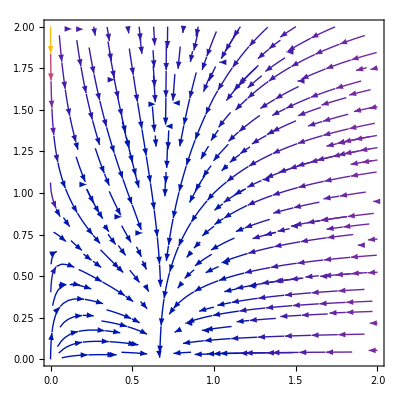

```mathematica
StreamPlot[Evaluate[gradGraves/.AB->3],{T,0,2},{P,0,2},PlotRangePadding->None]
```

Hashimoto treatment set AB<1 and B30>1
KX2=AB=0, KT=KP=1, B30>1
We expect a stable fixed point at (P=0, T=0)

```mathematica
gradHashimoto=Most@#/.Solve[#[[-1]],x2][[1]]&@(eq/.KX2|AB->0/.KT|KP->1/.x_[t]->x/.at|ap->1)//Quiet
```

{T (-1+1/3 (1-T) (-(2 B30)/T+(2^(1/3) B30^2)/((2 B30^3 T^3+27 P T^4+3 √3 √(4 B30^3 P T^7+27 P^2 T^8))^(1/3))+((2 B30^3 T^3+27 P T^4+3 √3 √(4 B30^3 P T^7+27 P^2 T^8))^(1/3))/(2^(1/3) T^2))),P (-1+((1-P) √((-(2 B30)/T+(2^(1/3) B30^2)/((2 B30^3 T^3+27 P T^4+3 √3 √(4 B30^3 P T^7+27 P^2 T^8))^(1/3))+((2 B30^3 T^3+27 P T^4+3 √3 √(4 B30^3 P T^7+27 P^2 T^8))^(1/3))/(2^(1/3) T^2))/P))/(√3))}

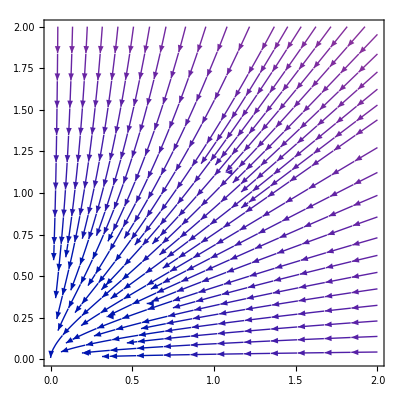

```mathematica
StreamPlot[Evaluate[gradHashimoto/.B30->2],{T,0,2},{P,0,2},PlotRangePadding->None]
```

Hashimoto weak treatment B30<1 and AB<1-(1-B30)/(B30^2 KP) 
KX2=AB=0, KT=KP=1, B30<1
We expect a stable fixed point at (P>0, T=0)

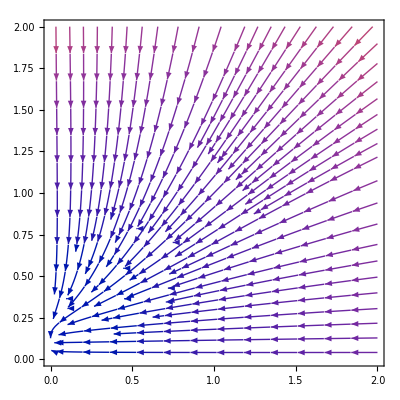

```mathematica
StreamPlot[Evaluate[gradHashimoto/.B30->.9],{T,0,2},{P,0,2},PlotRangePadding->None]
```

```mathematica
gradGeneral=Most@#/.Solve[#[[-1]],x2][[1]]&@(eq/.KX2->0/.x_[t]->x/.at|ap->1)//Quiet
```

{T (-1+(1-KT T) (AB-(2 (B30+AB T))/(3 T)-(2^(1/3) (-B30^2 T^2-2 AB B30 T^3-AB^2 T^4))/(3 T^2 (2 B30^3 T^3+6 AB B30^2 T^4+27 P T^4+6 AB^2 B30 T^5+2 AB^3 T^6+3 √3 √(4 B30^3 P T^7+12 AB B30^2 P T^8+27 P^2 T^8+12 AB^2 B30 P T^9+4 AB^3 P T^10))^(1/3))+((2 B30^3 T^3+6 AB B30^2 T^4+27 P T^4+6 AB^2 B30 T^5+2 AB^3 T^6+3 √3 √(4 B30^3 P T^7+12 AB B30^2 P T^8+27 P^2 T^8+12 AB^2 B30 P T^9+4 AB^3 P T^10))^(1/3))/(3 2^(1/3) T^2))),P (-1+(1-KP P) √((-(2 (B30+AB T))/(3 T)-(2^(1/3) (-B30^2 T^2-2 AB B30 T^3-AB^2 T^4))/(3 T^2 (2 B30^3 T^3+6 AB B30^2 T^4+27 P T^4+6 AB^2 B30 T^5+2 AB^3 T^6+3 √3 √(4 B30^3 P T^7+12 AB B30^2 P T^8+27 P^2 T^8+12 AB^2 B30 P T^9+4 AB^3 P T^10))^(1/3))+((2 B30^3 T^3+6 AB B30^2 T^4+27 P T^4+6 AB^2 B30 T^5+2 AB^3 T^6+3 √3 √(4 B30^3 P T^7+12 AB B30^2 P T^8+27 P^2 T^8+12 AB^2 B30 P T^9+4 AB^3 P T^10))^(1/3))/(3 2^(1/3) T^2))/P))}

```mathematica
Manipulate[Show[{StreamPlot[{T (-1+(1-KT T) (AB-(2 (B30+AB T))/(3 T)-(2^(1/3) (-B30^2 T^2-2 AB B30 T^3-AB^2 T^4))/(3 T^2 (2 B30^3 T^3+6 AB B30^2 T^4+27 P T^4+6 AB^2 B30 T^5+2 AB^3 T^6+3 √3 √(4 B30^3 P T^7+12 AB B30^2 P T^8+27 P^2 T^8+12 AB^2 B30 P T^9+4 AB^3 P T^10))^(1/3))+((2 B30^3 T^3+6 AB B30^2 T^4+27 P T^4+6 AB^2 B30 T^5+2 AB^3 T^6+3 √3 √(4 B30^3 P T^7+12 AB B30^2 P T^8+27 P^2 T^8+12 AB^2 B30 P T^9+4 AB^3 P T^10))^(1/3))/(3 2^(1/3) T^2))),P (-1+(1-KP P) √(1/P(-(2 (B30+AB T))/(3 T)-(2^(1/3) (-B30^2 T^2-2 AB B30 T^3-AB^2 T^4))/(3 T^2 (2 B30^3 T^3+6 AB B30^2 T^4+27 P T^4+6 AB^2 B30 T^5+2 AB^3 T^6+3 √3 √(4 B30^3 P T^7+12 AB B30^2 P T^8+27 P^2 T^8+12 AB^2 B30 P T^9+4 AB^3 P T^10))^(1/3))+((2 B30^3 T^3+6 AB B30^2 T^4+27 P T^4+6 AB^2 B30 T^5+2 AB^3 T^6+3 √3 √(4 B30^3 P T^7+12 AB B30^2 P T^8+27 P^2 T^8+12 AB^2 B30 P T^9+4 AB^3 P T^10))^(1/3))/(3 2^(1/3) T^2))))},{T,0,2},{P,0,2},PlotRangePadding->0.05,PerformanceGoal->"Quality",FrameLabel->{T,P}],
ContourPlot[{{T (-1+(1-KT T) (AB-(2 (B30+AB T))/(3 T)-(2^(1/3) (-B30^2 T^2-2 AB B30 T^3-AB^2 T^4))/(3 T^2 (2 B30^3 T^3+6 AB B30^2 T^4+27 P T^4+6 AB^2 B30 T^5+2 AB^3 T^6+3 √3 √(4 B30^3 P T^7+12 AB B30^2 P T^8+27 P^2 T^8+12 AB^2 B30 P T^9+4 AB^3 P T^10))^(1/3))+((2 B30^3 T^3+6 AB B30^2 T^4+27 P T^4+6 AB^2 B30 T^5+2 AB^3 T^6+3 √3 √(4 B30^3 P T^7+12 AB B30^2 P T^8+27 P^2 T^8+12 AB^2 B30 P T^9+4 AB^3 P T^10))^(1/3))/(3 2^(1/3) T^2)))==0, T==0}},{T,-0.1,2},{P,0,2},ContourStyle->{{Thickness[.01],Orange}},PerformanceGoal->"Quality"],ContourPlot[{{P (-1+(1-KP P) √(1/P(-(2 (B30+AB T))/(3 T)-(2^(1/3) (-B30^2 T^2-2 AB B30 T^3-AB^2 T^4))/(3 T^2 (2 B30^3 T^3+6 AB B30^2 T^4+27 P T^4+6 AB^2 B30 T^5+2 AB^3 T^6+3 √3 √(4 B30^3 P T^7+12 AB B30^2 P T^8+27 P^2 T^8+12 AB^2 B30 P T^9+4 AB^3 P T^10))^(1/3))+((2 B30^3 T^3+6 AB B30^2 T^4+27 P T^4+6 AB^2 B30 T^5+2 AB^3 T^6+3 √3 √(4 B30^3 P T^7+12 AB B30^2 P T^8+27 P^2 T^8+12 AB^2 B30 P T^9+4 AB^3 P T^10))^(1/3))/(3 2^(1/3) T^2))))==0, P==0}},{T,0,2},{P,-0.1,2},ContourStyle->{{Thickness[.01],Blue}},PerformanceGoal->"Quality"]
(*ParametricPlot[{0,P},{P,0,2},PlotStyle->{Orange,Thickness[.01]}],ParametricPlot[{T,0},{T,0,2},PlotStyle->{Blue,Thickness[.01]}],*)
}],
{KP,0,1},{KT,0,1},{AB,0,3},{B30,0,3}]
```

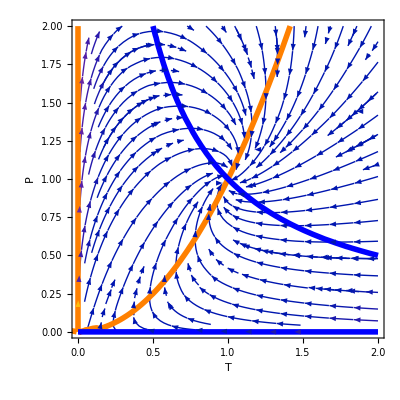
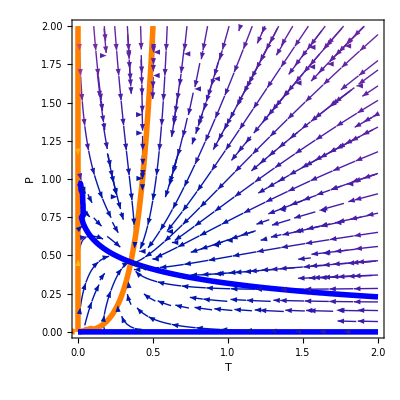
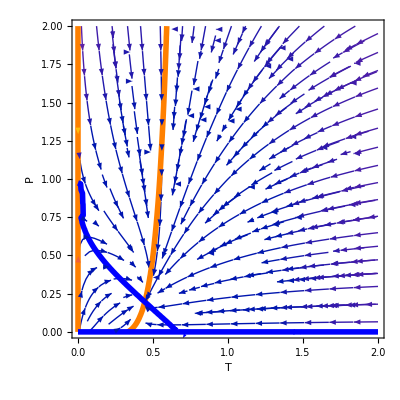
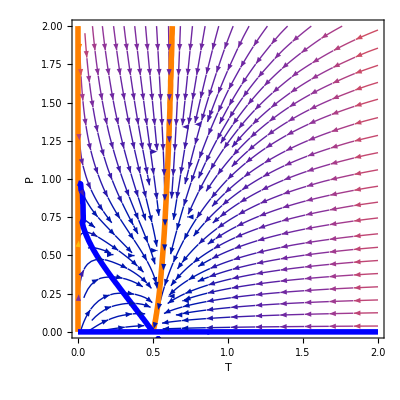
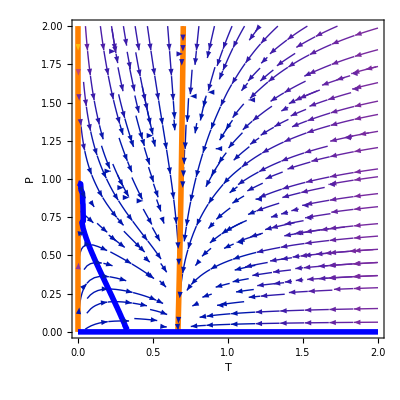
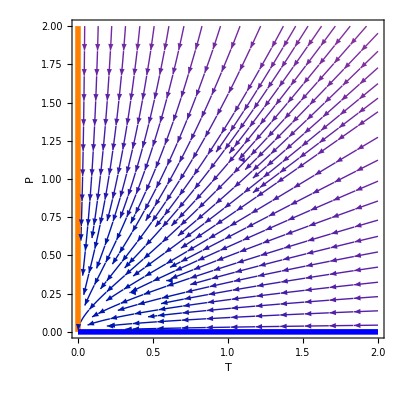
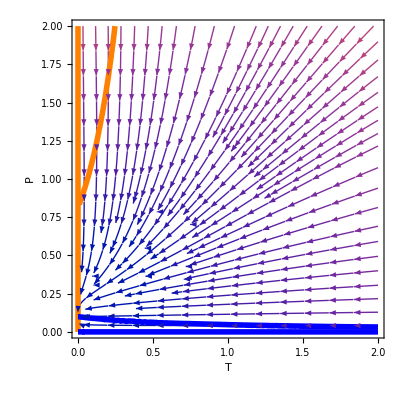
```mathematica
TableForm@{{-Graphics-,Thread[{KP,KT,AB,B30}-> {0,0,0,0}]},{-Graphics-,Thread[{KP,KT,AB,B30}-> {1,1,0,0}]},{-Graphics-,Thread[{KP,KT,AB,B30}->{1,1,1.5,0}]},{-Graphics-,Thread[{KP,KT,AB,B30}->{1,1,2,0}]},{-Graphics-,Thread[{KP,KT,AB,B30}->{1,1,3,0}]},{-Graphics-,Thread[{KP,KT,AB,B30}->{1,1,0,2}]},{-Graphics-,Thread[{KP,KT,AB,B30}->{1,1,0,0.9}]}}
```

-Graphics- | KP→0
KT→0
AB→0
B30→0
-Graphics- | KP→1
KT→1
AB→0
B30→0
-Graphics- | KP→1
KT→1
AB→1.5
B30→0
-Graphics- | KP→1
KT→1
AB→2
B30→0
-Graphics- | KP→1
KT→1
AB→3
B30→0
-Graphics- | KP→1
KT→1
AB→0
B30→2
-Graphics- | KP→1
KT→1
AB→0
B30→0.9

## Nullclines with hyperthyroidism and hypothyroidism ranges in Hashimoto’s thyroiditis, Graves’ disease, and iodine defficiency

### Computation of null clines

To compute the null clines dT/dt=0, dP/dt=0 in the general model we use the separation of time scales in the model - the hormone turnover times are much faster than the gland turnover times. We sepearte the model to the hormone “fast” equations (eqf) and the gland “slow” equations (eqs):

```mathematica
eqf={x1'==b1 u/x3-a1 x1,x2'==b2 P x1/x3-a2 x2,x3'==b3 T ((Ab+x2)/(1+kx2 (Ab+ x2)))-a3 x3};
eqs={T'==T (bt ((Ab+x2)/(1+kx2(Ab+ x2)))(1-kT T)-at),P'==P (bp/x3(1-kP P)-ap)};
```

We  first solve the steady-states for the hormone equations. The equations cannot be explicitly solved, therefore we express x1 and x3 using x2, and use an implicit equation for x2.

```mathematica
x1x3=Solve[#[[;;2]],{x1,x3}][[2]]&@(eqf/.x_'->0)
```

{x1→(√a2 √b1 √u √x2)/(√a1 √b2 √P),x3→(√b1 √b2 √P √u)/(√a1 √a2 √x2)}

```mathematica
eq2=FullSimplify[#[[3]]/.Solve[#[[;;2]],{x1,x3}][[2]]&@(eqf/.x_'->0)]
```

(b3 T (Ab+x2))/(1+kx2 (Ab+x2))==(a3 √b1 √b2 √P √u)/(√a1 √a2 √x2)

We substitute the “fast” equations steady-state in the slow equations to solve the null clines dT/dt=0 (ncT) and dP/dt=0 (ncP). One solution is T=0, P=0, respectively. The other soution is:

```mathematica
{ncT,ncP}=Refine[FullSimplify@Eliminate[{#,eq2},x2],a1≠0&&a2≠0&&b1≠0&&b2≠0&&u≠0]&/@(eqs/.x_'->0/.x1x3)
```

{a1 a2 at^2 b3^2 T^2 (at+Ab at kx2+Ab bt (-1+kT T))+a3^2 b1 b2 bt^2 P (-1+kT T)^2 (at kx2+bt (-1+kT T)) u==0,P (bp^2 (-1+kP P)^2 (a3 bp (1+Ab kx2) (-1+kP P)+Ab ap b3 T)+(ap^2 b1 b2 P (a3 bp kx2 (-1+kP P)+ap b3 T) u)/(a1 a2))==0}

### Computation of hypothyroid/ hyperthyroid ranges in the glands T-P plane

Here too we use the sepertion of time scales and assume the hormones are in steady-state. Thus, each choice of T,P (and the parameters) dictates x1, x2, x3.

```mathematica
Solve[(b3 T (Ab+x2))/(1+kx2 x2)== (a3 √b1 √b2 √P √u)/(√a1 √a2 √x2),T]
```

{{T→(a3 √b1 √b2 √P √u (1+kx2 x2))/(√a1 √a2 b3 √x2 (Ab+x2))}}

### Parameters for null cline and T4-TSH relation analysis

```mathematica
para={u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,at,bt,kP,ap,bp};
```

Values for the removal rates of the hormones/glands are taken from their turnover times
Values for the steady states of x2,x3 are the reference ranges for T4,TSH. TRH basal level was taken to be 1. gland steady-state sizes were taken to be 1.
Values for the carrying capacity of the glands: Thyroid - following Liu et al 2013. Pituitary - following Khawaja et al 2006.
Production rates were calibrated to give the defined steady-states for the hormones and glands.

Production rates calibration:

```mathematica
Solve[Join[eqf,eqs]/.x_'->0/.Ab->0/.kx2->0/.u->1/.{x2-> 1.5,x3-> 15,T-> 1,P-> 1,x1->1}/.{a1->250,a2->25,a3->1/7,at-> 1/30,ap->1/30,kT-> 1/5.5,kP-> 1/5.3},{b1,b2,b3,bt,bp}]
```

{{b1→3750,b2→562.5,b3→1.42857,bt→0.0271605,bp→0.616279}}

```mathematica
realparameters={u-> 1,a1->250.,a2->25.,a3->1/7,kx2->0,Ab->0,kT->1/5.5,at->1/30,kP->1/5.3,ap->1/30,b1->3750,b2->562.5,b3->1.4285714285714286,bt->0.027160493827160497,bp->0.6162790697674418};
```

### Hashimoto’s thyroiditis

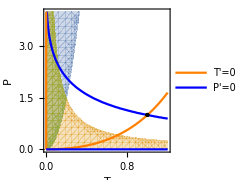
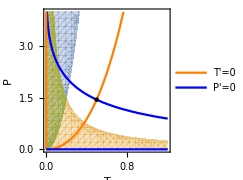
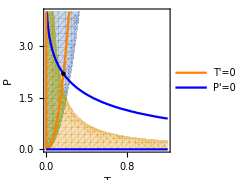
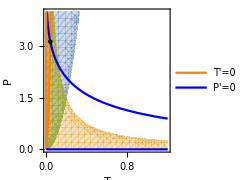

```mathematica
With[{Pmax=4,Tmax=1.2,u= 1,a1=250.,a2=25.,a3=1/7,kx2=0,Ab=0,kT=1/5.5,at=1/30,kP=1/5.3,ap=1/30,b1=3750,b2=562.5,b3=1.4285714285714286,bt=0.027160493827160497,bp=0.6162790697674418,vars={x1,x2,x3,T,P}},
Table[stst=NSolve[{0==-a1 x1+(b1 u)/x3,0==-a2 x2+(b2 P x1)/x3,0==b3 T ((Ab+x2)/(1+kx2 x2))-a3 x3,0==T (-at+bt (1-kT T) ((Ab+x2)/(1+kx2 x2))),0==P (-ap+(bp (1-kP P))/x3),x2>0,x3>0},vars,Reals];
Thread[{x2hypothyroidism, x2hyperthyroidism, x3hypothyroidism, x3hyperthyroidism}={5,0.5,10,20}];
Show[RegionPlot[{(*Evaluate[T>(a3 √b1 √b2 √P √u (1+kx2 x2))/(√a1 √a2 b3 √x2 (Ab+x2))/.x2->x2hyperthyroidism],*)
Evaluate[T<(a3 √b1 √b2 √P √u (1+kx2 x2))/(√a1 √a2 b3 √x2 (Ab+x2))/.x2->x2hypothyroidism],
Evaluate[T<(a3 √b1 √b2 √P √u (1+kx2 x2))/(√a1 √a2 b3 √x2 (Ab+x2))/.x2->(b1 b2 P u)/(a1 a2 x3^2)/.x3-> x3hypothyroidism],
Evaluate[(T<(a3 √b1 √b2 √P √u (1+kx2 x2))/(√a1 √a2 b3 √x2 (Ab+x2))/.x2->(b1 b2 P u)/(a1 a2 x3^2)/.x3-> x3hypothyroidism)&&(T<(a3 √b1 √b2 √P √u (1+kx2 x2))/(√a1 √a2 b3 √x2 (Ab+x2))/.x2->x2hypothyroidism)](*,
Evaluate[T>(a3 √b1 √b2 √P √u (1+kx2 x2))/(√a1 √a2 b3 √x2 (Ab+x2))/.x2->(b1 b2 P u)/(a1 a2 x3^2)/.x3-> x3hyperthyroidism]*)},{T,0,Tmax},{P,0,Pmax},PlotRange->All,(*PlotStyle->{Blue,Directive[ Orange,Opacity[.5]]},*)BoundaryStyle->None, Mesh->None],
(*StreamPlot[
f[parameters,{T,P}],{T,0.01,Tmax},{P,0.01,Pmax},
FrameLabel->{"T","P"}]//Quiet,*)
ContourPlot[
{Evaluate[(a^2 a1 a2 b3^2 T^2 (a+Ab bt (-1+kT T))+a3^2 b1 b2 bt^2 P (-1+kT T)^2 (a kx2+bt (-1+kT T)) u==0)],
P (bp^2 (-1+kP P)^2 (a3 bp (-1+kP P)+Ab ap b3 T)+(ap^2 b1 b2 P (a3 bp kx2 (-1+kP P)+ap b3 T) u)/(a1 a2))==0},
{T,0,Tmax},{P,0,Pmax},PlotRange->{{0,Tmax},{0,Pmax}},PerformanceGoal->"Quality",PlotLegends->Placed[{"T'=0","P'=0"},Below],ContourStyle->{Orange,Blue}],
ParametricPlot[{0,P},{P,0,Pmax},PlotStyle->Orange],ParametricPlot[{T,0},{T,0,Tmax},PlotStyle->Blue],
ListPlot[NSolve[{0==-a1 x1+(b1 u)/x3,0==-a2 x2+(b2 P x1)/x3,0==b3 T ((Ab+x2)/(1+kx2 x2))-a3 x3,0==T (-a+bt (1-kT T) ((Ab+x2)/(1+kx2 x2))),0==P (-ap+(bp (1-kP P))/x3),x2>0,x3>0},vars,Reals][[;;,{4,5},2]],PlotStyle->{Black,PointSize[Large]}]
,
Frame->True,FrameLabel->{"T","P"},AspectRatio->1,PlotRange->{{0,Tmax},{0,Pmax}},ImageSize->Small]
,{a,{at,2at,5at,15at}}]
]
```

```mathematica
Export["nullclines with clinical subclinical ranges for different at values - 30_3_2021.pdf",{{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}]
```

nullclines with clinical subclinical ranges for different at values - 30_3_2021.pdf

```mathematica
(P (bp^2 (-1+kP P)^2 (a3 bp (-1+kP P)+Ab ap b3 T)+(ap^2 b1 b2 P (a3 bp kx2 (-1+kP P)+ap b3 T) u)/(a1 a2))==0)/.{u->1,Ab->0,a1->1,a2->1,a3->1,b1->1,b2->1,b3->1,kx2->0,ap-> 1,bp->1}
```

P ((-1+kP P)^3+P T)==0

```mathematica
-1/P(-1+kP P)^3= T
```

### Graves’ disease

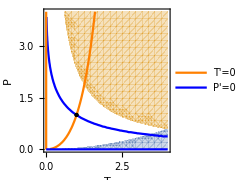
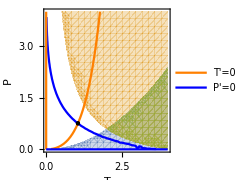
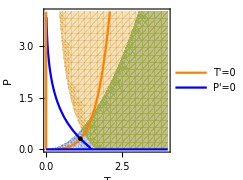
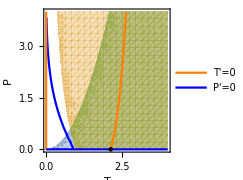

```mathematica
With[{Pmax=4,Tmax=4,u= 1,a1=250.,a2=25.,a3=1/7,kx2=0,Ab=0,kT=1/5.5,at=1/30,kP=1/5.3,ap=1/30,b1=3750,b2=562.5,b3=1.4285714285714286,bt=0.027160493827160497,bp=0.6162790697674418,vars={x1,x2,x3,T,P}},
{stst=NSolve[{0==-a1 x1+(b1 u)/x3,0==-a2 x2+(b2 P x1)/x3,0==b3 T ((Ab+x2)/(1+kx2 x2))-a3 x3,0==T (-at+bt (1-kT T) ((Ab+x2)/(1+kx2 x2))),0==P (-ap+(bp (1-kP P))/x3),x2≥ 0,x3>0},vars,Reals];Thread[{x2hypothyroidism, x2hyperthyroidism, x3hypothyroidism, x3hyperthyroidism}={5,0.5,10,20}];
Table[
Show[{RegionPlot[{Evaluate[T>(a3 √b1 √b2 √P √u (1+kx2 x2))/(√a1 √a2 b3 √x2 (Abnew+x2))/.x2->x2hyperthyroidism],
(*Evaluate[T<(a3 √b1 √b2 √P √u (1+kx2 x2))/(√a1 √a2 b3 √x2 (Abnew+x2))/.x2->x2hypothyroidism],*)
(*Evaluate[T<(a3 √b1 √b2 √P √u (1+kx2 x2))/(√a1 √a2 b3 √x2 (Abnew+x2))/.x2->(b1 b2 P u)/(a1 a2 x3^2)/.x3-> x3hypothyroidism],*)
Evaluate[T>(a3 √b1 √b2 √P √u (1+kx2 x2))/(√a1 √a2 b3 √x2 (Abnew+x2))/.x2->(b1 b2 P u)/(a1 a2 x3^2)/.x3-> x3hyperthyroidism],
Evaluate[(T>(a3 √b1 √b2 √P √u (1+kx2 x2))/(√a1 √a2 b3 √x2 (Abnew+x2))/.x2->x2hyperthyroidism)&&(T>(a3 √b1 √b2 √P √u (1+kx2 x2))/(√a1 √a2 b3 √x2 (Abnew+x2))/.x2->(b1 b2 P u)/(a1 a2 x3^2)/.x3-> x3hyperthyroidism)]},{T,0,Tmax},{P,0,Pmax},PlotRange->All(*,PlotStyle->{  LightBlue,LightBlue,Directive[ LightOrange,Opacity[.5]],Directive[LightOrange,Opacity[.5]]}*),BoundaryStyle->None],
(*StreamPlot[
f[parameters,{T,P}],{T,0.01,Tmax},{P,0.01,Pmax},
FrameLabel->{"T","P"}]//Quiet,*)
ContourPlot[
{Evaluate[(a1 a2 at^2 b3^2 T^2 (at+Abnew bt (-1+kT T))+a3^2 b1 b2 bt^2 P (-1+kT T)^2 (at kx2+bt (-1+kT T)) u==0)],
Evaluate[(P (bp^2 (-1+kP P)^2 (a3 bp (-1+kP P)+Abnew ap b3 T)+(ap^2 b1 b2 P (a3 bp kx2 (-1+kP P)+ap b3 T) u)/(a1 a2))==0)]},
{T,0.01,Tmax},{P,0.01,Pmax},PlotRange->{{0,Tmax},{0,Pmax}},PerformanceGoal->"Quality",PlotLegends->Placed[{"T'=0","P'=0"},Below],ContourStyle->{Orange,Blue,Orange,Blue}],
ParametricPlot[{0,P},{P,0,Pmax},PlotStyle->Orange],ParametricPlot[{T,0},{T,0,Tmax},PlotStyle->Blue],ListPlot[{{T,P}/.NSolve[{0==-a1 x1+(b1 u)/x3,0==-a2 x2+(b2 P x1)/x3,0==b3 T ((Abnew+x2)/(1+kx2 x2))-a3 x3,0==T (-at+bt (1-kT T) ((Abnew+x2)/(1+kx2 x2))),0==P (-ap+(bp (1-kP P))/x3),x2≥ 0,x3≥ 0,T≥ 1},vars,Reals][[1]]},PlotStyle->{Black,PointSize[Large]}]},
Frame->True,FrameLabel->{"T","P"},AspectRatio->1,PlotRange->{{0,Tmax},{0,Pmax}},ImageSize->Small]
,{Abnew,{0,0.5,1.2,2}}]
}]
```

```mathematica
Export["null clines with clinical subclinical - Graves - 21_12_2021.pdf",{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

null clines with clinical subclinical - Graves - 21_12_2021.pdf

### Iodine defficiency

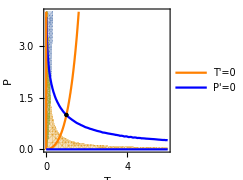
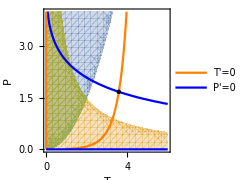
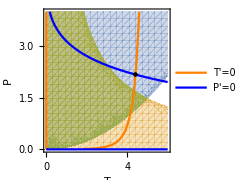
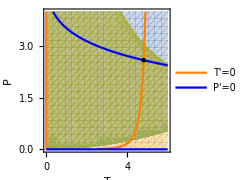

```mathematica
With[{Pmax=4,Tmax=6,u= 1,a1=250.,a2=25.,a3=1/7,kx2=0,Ab=0,kT=1/5.5,at=1/30,kP=1/5.3,ap=1/30,b1=3750,b2=562.5,b3=1.4285714285714286,bt=0.027160493827160497,bp=0.6162790697674418,vars={x1,x2,x3,T,P}},
{(*ststline=Table[NSolve[{0==-a1 x1+(b1 u)/x3,0==-a2 x2+(b2 P x1)/x3,0==b3line T ((Ab+x2)/(1+kx2 x2))-a3 x3,0==T (-at+bt (1-kT T) ((Ab+x2)/(1+kx2 x2))),0==P (-ap+(bp (1-kP P))/x3),x2≥ 0,x3>0},vars,Reals],{b3line,{0.01b3,0.05b3,0.1 b3,0.2 b3,0.30000000000000004 b3,0.4 b3,0.5 b3,0.6000000000000001 b3,0.7000000000000001 b3,0.8 b3,0.9 b3,1. b3}}][[;;,1,4;;5,2]];*)
stst=NSolve[{0==-a1 x1+(b1 u)/x3,0==-a2 x2+(b2 P x1)/x3,0==b3 T ((Ab+x2)/(1+kx2 x2))-a3 x3,0==T (-at+bt (1-kT T) ((Ab+x2)/(1+kx2 x2))),0==P (-ap+(bp (1-kP P))/x3),x2≥ 0,x3>0},vars,Reals];Thread[{x2hypothyroidism, x2hyperthyroidism, x3hypothyroidism, x3hyperthyroidism}={5,0.5,10,20}];
Table[
Show[{RegionPlot[{(*Evaluate[T>(a3 √b1 √b2 √P √u (1+kx2 x2))/(√a1 √a2 b3new √x2 (Ab+x2))/.x2->x2hyperthyroidism],*)
Evaluate[T<(a3 √b1 √b2 √P √u (1+kx2 x2))/(√a1 √a2 b3new √x2 (Ab+x2))/.x2->x2hypothyroidism],
Evaluate[T<(a3 √b1 √b2 √P √u (1+kx2 x2))/(√a1 √a2 b3new √x2 (Ab+x2))/.x2->(b1 b2 P u)/(a1 a2 x3^2)/.x3-> x3hypothyroidism],
Evaluate[(T<(a3 √b1 √b2 √P √u (1+kx2 x2))/(√a1 √a2 b3new √x2 (Ab+x2))/.x2->x2hypothyroidism)&&(T<(a3 √b1 √b2 √P √u (1+kx2 x2))/(√a1 √a2 b3new √x2 (Ab+x2))/.x2->(b1 b2 P u)/(a1 a2 x3^2)/.x3-> x3hypothyroidism)]
(*Evaluate[T>(a3 √b1 √b2 √P √u (1+kx2 x2))/(√a1 √a2 b3new √x2 (Ab+x2))/.x2->(b1 b2 P u)/(a1 a2 x3^2)/.x3-> x3hyperthyroidism]*)},{T,0,Tmax},{P,0,Pmax},PlotRange->All,(*PlotStyle->{  LightBlue,LightBlue,Directive[ LightOrange,Opacity[.5]],Directive[LightOrange,Opacity[.5]]},*)BoundaryStyle->None],
(*StreamPlot[
f[parameters,{T,P}],{T,0.01,Tmax},{P,0.01,Pmax},
FrameLabel->{"T","P"}]//Quiet,*)
ContourPlot[
{Evaluate[(a1 a2 at^2 b3new^2 T^2 (at+Ab bt (-1+kT T))+a3^2 b1 b2 bt^2 P (-1+kT T)^2 (at kx2+bt (-1+kT T)) u==0)],
Evaluate[P (bp^2 (-1+kP P)^2 (a3 bp (-1+kP P)+Ab ap b3new T)+(ap^2 b1 b2 P (a3 bp kx2 (-1+kP P)+ap b3new T) u)/(a1 a2))==0]},
{T,0.01,Tmax},{P,0.01,Pmax},PlotRange->{{0,Tmax},{0,Pmax}},PerformanceGoal->"Quality",PlotLegends->Placed[{"T'=0","P'=0"},Below],ContourStyle->{Orange,Blue,Orange,Blue}],
ParametricPlot[{0,P},{P,0,Pmax},PlotStyle->Orange],ParametricPlot[{T,0},{T,0,Tmax},PlotStyle->Blue](*,
ListLinePlot[ststline,PlotStyle->Black]*),
ListPlot[{{T,P}/.NSolve[{0==-a1 x1+(b1 u)/x3,0==-a2 x2+(b2 P x1)/x3,0==b3new T ((Ab+x2)/(1+kx2 x2))-a3 x3,0==T (-at+bt (1-kT T) ((Ab+x2)/(1+kx2 x2))),0==P (-ap+(bp (1-kP P))/x3),x2≥ 0,x3≥ 0},vars,Reals][[1]]},PlotStyle->{Black,PointSize[Large]}]},
Frame->True,FrameLabel->{"T","P"},AspectRatio->1,PlotRange->{{0,Tmax},{0,Pmax}},ImageSize->Small]
,{b3new,{b3,0.1b3,0.04b3,0.02b3}}]
}]
```

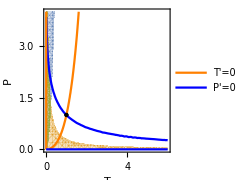
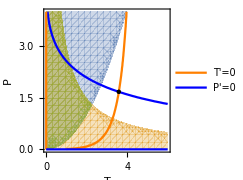
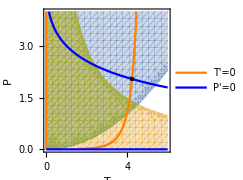
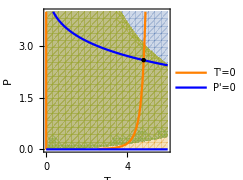
```mathematica
Export["null clines with clinical subclinical - iodine defficiency 21_12_2021.pdf",{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

null clines with clinical subclinical - iodine defficiency 21_12_2021.pdf

## TSH-T4 Relation

Computation of TSH-T4 relation in the model:

From the st. st. of the equations for x1, x2 and P we get:
{-a1 x1[t]+(b1 u)/x3[t]==0 ,-a2 x2[t]+(b2 P[t]x1[t])/x3[t]==0 ,P[t] (-ap+(bp (1-kP P[t]))/x3[t])==0}
x1[t]=(b1 u)/(a1 x3[t])
P[t]=(bp-ap x3[t])/(bp kP) for x3<bp/ap or P = 0 for  x3>bp/ap
Substituing x1 and P in x2 :
x2[t]=(b1 b2 u)/(a1 a2  kP)(1-ap/bp x3[t])/x3[t]^2 for x3<bp/ap or x2[t] = 0 for  x3>bp/ap
Summing up, there are two solutions for x2(x3) and P(x3):
x3<=bp/ap: x2 = (b1 b2 u)/(a1 a2  kP)(1-ap/bp x3)/x3^2 (and P=(bp-ap x3)/(bp kP))
x3>bp/ap: x2 = 0 (and P=0)

```mathematica
para={u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,at,bt,kP,ap,bp}
```

{u,a1,b1,a2,b2,a3,b3,kx2,Ab,kT,at,bt,kP,ap,bp}

```mathematica
realparameters={u-> 1,a1->250.,a2->25.,a3->1/7,kx2->0,Ab->0,kT->1/5.5,at->1/30,kP->1/5.3,ap->1/30,b1->3750,b2->562.5,b3->1.4285714285714286,bt->0.027160493827160497,bp->0.6162790697674418}
```

{u→1,a1→250.,a2→25.,a3→1/7,kx2→0,Ab→0,kT→0.181818,at→1/30,kP→0.188679,ap→1/30,b1→3750,b2→562.5,b3→1.42857,bt→0.0271605,bp→0.616279}

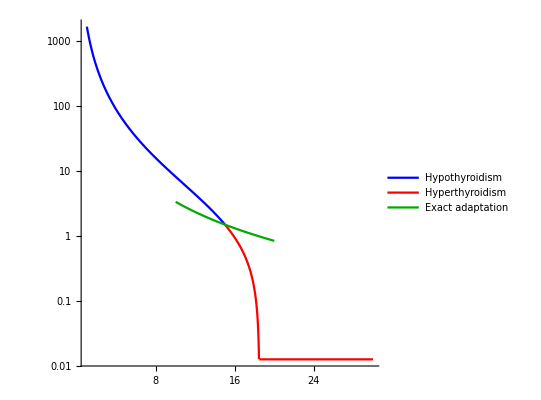

```mathematica
Show[{LogPlot[(b1 b2 u)/(a1 a2  kP)(1-ap/bp x3)/x3^2/.realparameters,{x3,1,15},AspectRatio->1,PlotStyle->Blue,PlotLegends-> {"Hypothyroidism"},AxesOrigin-> {0,0.01}],
LogPlot[(b1 b2 u)/(a1 a2  kP)(1-ap/bp x3)/x3^2/.realparameters,{x3,15,0.6162790697674418/(1/30)+0.1},AspectRatio->1,PlotStyle->Red,PlotLegends-> {"Hyperthyroidism"}],
LogPlot[10^-1.9,{x3,0.6162790697674418/(1/30),30},AspectRatio->1,PlotStyle->Red],
LogPlot[(15^2 1.5)/T4^2,{T4,10,20},AspectRatio->1,PlotStyle->Darker@Green,PlotLegends-> {"Exact adaptation"}](*,
ListLogPlot[Select[Graves,#[[1]]>15&],AspectRatio->1, Joined->True,PlotStyle->Red,PlotLegends-> {"Hyperthyroidism"}],
LogPlot[(15^2 1.5)/T4^2,{T4,10,20},AspectRatio->1,PlotStyle->Darker@Green,PlotLegends-> {"Exact adaptation"}],
ListLogPlot[{{15,1.5}}]*)},
PlotRange-> All
]
```

```mathematica
Export["log linear line model.pdf",-Graphics-]
```

log linear line model.pdf

### Overlay with Midgley 2013 data

We fit the model to data from Midgley 2013 PMID : 23423518.
Data was extracted using the WebPlotDigitizer software .

```mathematica
midgley=Import["C:\\Users\\yaelko\\Box\\hpt axis\\log linear datasets\\midgley.csv"];
```

```mathematica
midgley2=Select[midgley,0<#[[1]]<51&& 0.008<#[[2]]<105 &];
```

```mathematica
logmidgley2={midgley2[[;;,1]],Log10@midgley2[[;;,2]]}ᵀ;
```

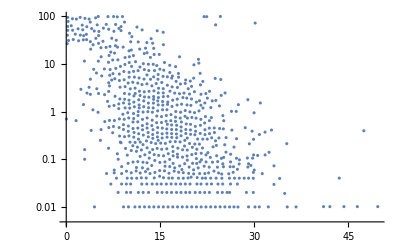
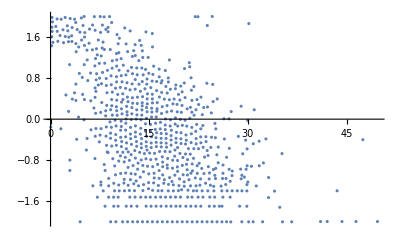

```mathematica
{ListLogPlot[midgley2],ListPlot[logmidgley2]}
```

We fit the data to equation: x2 = (b1 b2 u)/(a1 a2  kP)(1-ap/bp x3)/x3^2
Defining:
α = (b1 b2 u)/(a1 a2  kP)
β = ap/bp
The equation becomes:
x2 = α(1-β x3)/x3^2
In the model without carrying capacities, the steady-state can be solved analytically:  {x1_0→(ap b1 u)/(a1 bp),x2_0→at/bt,x3_0→bp/ap,T_0→(a3 bp bt)/(ap at b3),P_0→(a1 a2 at bp^2)/(ap^2 b1 b2 bt u)}
Therefore, α,β can be rewritten as:
α = (x2_0 x3_0^2)/(P_0 kP)
β = 1/x3_0
Note that x10 x20 etc are not the steady-state for the full system with carrying capacitites.
Assuming that in the normal set-point the glands are far from their carrying capacities, we can thus compute α,β. We consider a normal set-point of FT4 x3_0=15pmol/L, and TSH x2_0=1.5mIU/L, and we normalize the pituitary mass units so that in the normal set point  P_0=1.
Therefore:
α = 337.5/(P_0 kP)
β = 1/15
We take Kp=P_0/5 following Khawaja:

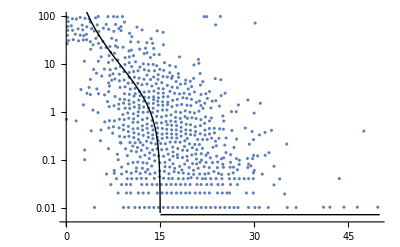

```mathematica
Show[ListLogPlot[midgley2,AxesOrigin-> {0,0.005}],LogPlot[Evaluate[(UnitStep[1-β x3]α (1-β x3)/x3^2+UnitStep[β x3-1] 10^-2.15)/.{α->1.5 15^2/0.2, β->1/15}],{x3,2,50},PlotRange->All,PlotStyle->{Black,Thick}]]
```

```mathematica
Export["overlay model with Midgley 2013.pdf",-Graphics-]
```

overlay model with Midgley 2013.pdf

## Dependence on antibody parameter in Graves’ disease

To analytically explore the model dynamics under pertrubation of the Ab parameter in Graves’ diseases, we considered the following equations:

x1'[t]==(b1 u)/x3[t]-a1 x1[t]
x2'[t]==(b2 P[t] x1[t])/x3[t]-a2 x2[t]
x3'[t]==b3 T[t] (Ab+x2[t])-a3 x3[t]
T'[t]==T[t] (bt (1-kT T[t]) (Ab+x2[t])-at)
P'[t]==P[t] (bp/x3[t]-ap)

Note that to allow analytical solution, we considered here a linear dependence between x3 and x2. We also assume here that the pituitary gland P is far from its carrying capacity (since in hyperthyroidism P shrinks).

Solving the fast equations for dx1/dt, dx2/dt, dx3/dt gives:

```mathematica
gravesststfun[a1_,a2_,a3_,b1_,b2_,b3_,Ab_,u_]:=Thread[{x1[t],x2[t],x3[t]}->( {(b1 u)/(a1 x3[t]),(b1 b2 u P[t])/(a1 a2 x3[t]^2),x3[t]}/.x3[t]->1/3 ((Ab b3 T[t])/a3+(2^(1/3) a1 a2 Ab^2 b3^2 T[t]^2)/(a3 (27 a1^2 a2^2 a3^2 b1 b2 b3 u P[t] T[t]+2 a1^3 a2^3 Ab^3 b3^3 T[t]^3+3 √3 √(27 a1^4 a2^4 a3^4 b1^2 b2^2 b3^2 u^2 P[t]^2 T[t]^2+4 a1^5 a2^5 a3^2 Ab^3 b1 b2 b3^4 u P[t] T[t]^4))^(1/3))+((27 a1^2 a2^2 a3^2 b1 b2 b3 u P[t] T[t]+2 a1^3 a2^3 Ab^3 b3^3 T[t]^3+3 √3 √(27 a1^4 a2^4 a3^4 b1^2 b2^2 b3^2 u^2 P[t]^2 T[t]^2+4 a1^5 a2^5 a3^2 Ab^3 b1 b2 b3^4 u P[t] T[t]^4))^(1/3))/(2^(1/3) a1 a2 a3)))]
```

```mathematica
{x1'[t]==-a1 x1[t]+(b1 u)/x3[t],x1[0]== x11,
x2'[t]==-a2 x2[t]+(b2 P[t] x1[t])/x3[t],x2[0]== x20,
x3'[t]==b30+b3 T[t] ((Ab+x2[t])/(1+kx2 (Ab+x2[t])))-a3 x3[t],x3[0]== x30,
T'[t]==T[t] (-at+bt (1-kT T[t]) ((Ab+x2[t])/(1+kx2 (Ab+x2[t])))),T[0]== T0,
P'[t]==P[t] (-ap+(bp (1-kP P[t]))/x3[t]),P[0]== P0
}[[;;;;2]]/.kP|kx2|b30->0/.Alternatives@@{a1,a2,b1,b2,u}->1/.x_'[t]->0/.x_[t]->x/.x1->1/x3/.x2->P/x3^2
```

{True,True,0==b3 T (Ab+P/x3^2)-a3 x3,0==T (-at+bt (1-kT T) (Ab+P/x3^2)),0==P (-ap+bp/x3)}

```mathematica
Solve[{0==b3 T (Ab+P/x3^2)-a3 x3,0==T (-at+bt (1-kT T) (Ab+P/x3^2)),0==P (-ap+bp/x3)},{T,P,x3}]
```

{{T→(a3 bp bt)/(ap at b3+a3 bp bt kT),P→-(bp^2 (-ap at b3+Ab ap b3 bt-a3 bp bt kT))/(ap^3 b3 bt),x3→bp/ap},{T→(-at+Ab bt)/(Ab bt kT),P→0,x3→(b3 (-at+Ab bt))/(a3 bt kT)}}

```mathematica
{0==T (Ab+P/x3^2)-x3,0==T (-1+(1-kT T) (Ab+P/x3^2)),0==P (-1+1/x3)}/.x3->1
```

{0==-1+(Ab+P) T,0==T (-1+(Ab+P) (1-kT T)),True}

```mathematica
x1'[t]==(b1 u)/x3[t]-a1 x1[t]
x2'[t]==(b2 P[t] x1[t])/x3[t]-a2 x2[t]
x3'[t]==b3 T[t] (Ab+x2[t])-a3 x3[t]
T'[t]==T[t] (bt (1-kT T[t]) (Ab+x2[t])-at)
P'[t]==P[t] (bp/x3[t]-ap)
```

```mathematica
Solve[{T[t](bt (x2[t]+Ab)(1-kT T[t])-at)==0,P[t](bp/x3[t]-ap)==0}/.gravesststfun[a1,a2,a3,b1,b2,b3,Ab,u],{T[t],P[t]}]
```

Substituing this into the equations for dT/dt, dP/dt gives two solutions:
(1){T[t]→1/kT(1-at/(Ab bt)),P[t]→0}
(2) {T[t]→1/((ap at b3)/(a3 bp bt)+kT),P[t]→(a1 a2 bp^2)/(ap^3 b1 b2 b3 u)(ap b3 (at/bt-Ab)+a3 bp kT)}

```mathematica
Solve[{T[t](bt (x2[t]+Ab)(1-kT T[t])-at)==0,P[t](bp/x3[t]-ap)==0}/.gravesststfun[a1,a2,a3,b1,b2,b3,Ab,u],{T[t],P[t]}]
```

{{T[t]→(-at+Ab bt)/(Ab bt kT),P[t]→0},{T[t]→(a3 bp bt)/(ap at b3+a3 bp bt kT),P[t]→-(a1 a2 bp^2 (-ap at b3+Ab ap b3 bt-a3 bp bt kT))/(ap^3 b1 b2 b3 bt u)}}

When Ab<=at/bt, we get only one fixed point, at {T[t]→1/((ap at b3)/(a3 bp bt)+kT),P[t]→(a1 a2 bp^2)/(ap^3 b1 b2 b3 u)(ap b3 (at/bt-Ab)+a3 bp kT)}, and T,x3 are compenstaed (i.e. they are independent of Ab). Above this value, another unstable fixed point at {T[t]→1/kT(1-at/(Ab bt)),P[t]→0} appears - but T and x3 are still compensated. 
When Ab>at/bt+(a3 bp kT)/(ap b3), the stable fixed point at {T[t]→1/((ap at b3)/(a3 bp bt)+kT),P[t]→(a1 a2 bp^2)/(ap^3 b1 b2 b3 u)(ap b3 (at/bt-Ab)+a3 bp kT)} is lost, and the fixed point at {T[t]→1/kT(1-at/(Ab bt)),P[t]→0} becomes stable. Now T and x3 start to depend on Ab, and rise gradually together. 
With the first fixed point, x3 value is x3=(b3 (-at+Ab bt))/(a3 bt kT) -> linear dependence on Ab. With the second one,

```mathematica
PowerExpand@FullSimplify[1/3 ((Ab b3 T[t])/a3+(2^(1/3) a1 a2 Ab^2 b3^2 T[t]^2)/(a3 (27 a1^2 a2^2 a3^2 b1 b2 b3 u P[t] T[t]+2 a1^3 a2^3 Ab^3 b3^3 T[t]^3+3 √3 √(27 a1^4 a2^4 a3^4 b1^2 b2^2 b3^2 u^2 P[t]^2 T[t]^2+4 a1^5 a2^5 a3^2 Ab^3 b1 b2 b3^4 u P[t] T[t]^4))^(1/3))+1/(2^(1/3) a1 a2 a3)(27 a1^2 a2^2 a3^2 b1 b2 b3 u P[t] T[t]+2 a1^3 a2^3 Ab^3 b3^3 T[t]^3+3 √3 √(27 a1^4 a2^4 a3^4 b1^2 b2^2 b3^2 u^2 P[t]^2 T[t]^2+4 a1^5 a2^5 a3^2 Ab^3 b1 b2 b3^4 u P[t] T[t]^4))^(1/3))/.{T[t]-> 1/kT(1-at/(Ab bt)),P[t]-> 0}]
```

(b3 (-at+Ab bt))/(a3 bt kT)

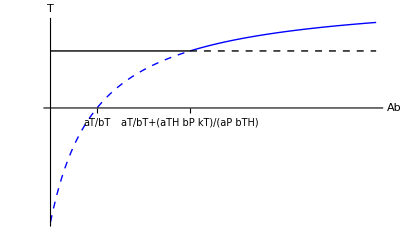

```mathematica
With[{at=1,bt=1, cT=1, ap=1,bp=1,kP=1,kT=1,a1=1,a2=1,a3=1,b1=1,b2=1,b3=1,u=1},
Show[Plot[{1/kT(1-at/(Ab bt)),1/((ap at b3)/(a3 bp bt)+kT)},{Ab,0.5,2},PlotRange->All,PlotStyle->{{Blue,Dashed,Thick},{Black,Thick}}],
Plot[{1/kT(1-at/(Ab bt)),1/((ap at b3)/(a3 bp bt)+kT)},{Ab,2,4},PlotRange->All,PlotStyle->{{Blue,Thick},{Black,Dashed,Thick}}],
AxesLabel-> {"Ab","T"},Ticks->{{{1,"aT/bT"},{2,"aT/bT+(aTH bP kT)/(aP bTH)"}},None}]]
```

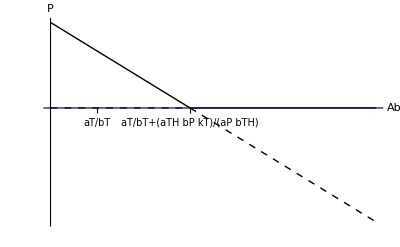

```mathematica
With[{at=1,bt=1, cT=1, ap=1,bp=1,kP=1,kT=1,a1=1,a2=1,a3=1,b1=1,b2=1,b3=1,u=1},
Show[Plot[{0,(a1 a2 bp^2)/(ap^3 b1 b2 b3 u)(ap b3 (at/bt-Ab)+a3 bp kT)},{Ab,0.5,2},PlotRange->All,PlotStyle->{{Blue,Dashed,Thick},{Black,Thick}}],
Plot[{0,(a1 a2 bp^2)/(ap^3 b1 b2 b3 u)(ap b3 (at/bt-Ab)+a3 bp kT)},{Ab,2,4},PlotRange->All,PlotStyle->{{Blue,Thick},{Black,Dashed,Thick}}],
AxesLabel-> {"Ab","P"},Ticks->{{{1,"aT/bT"},{2,"aT/bT+(aTH bP kT)/(aP bTH)"}},None}]]
```

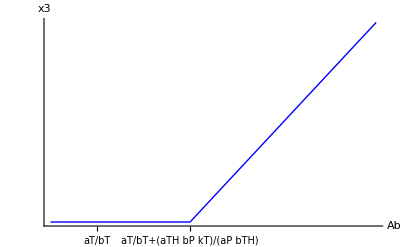

```mathematica
With[{at=1,bt=1, cT=1, ap=1,bp=1,kP=1,kT=1,a1=1,a2=1,a3=1,b1=1,b2=1,b3=1,u=1},
Show[Plot[1/3 ((Ab b3 T[t])/a3+(2^(1/3) a1 a2 Ab^2 b3^2 T[t]^2)/(a3 (27 a1^2 a2^2 a3^2 b1 b2 b3 u P[t] T[t]+2 a1^3 a2^3 Ab^3 b3^3 T[t]^3+3 √3 √(27 a1^4 a2^4 a3^4 b1^2 b2^2 b3^2 u^2 P[t]^2 T[t]^2+4 a1^5 a2^5 a3^2 Ab^3 b1 b2 b3^4 u P[t] T[t]^4))^(1/3))+((27 a1^2 a2^2 a3^2 b1 b2 b3 u P[t] T[t]+2 a1^3 a2^3 Ab^3 b3^3 T[t]^3+3 √3 √(27 a1^4 a2^4 a3^4 b1^2 b2^2 b3^2 u^2 P[t]^2 T[t]^2+4 a1^5 a2^5 a3^2 Ab^3 b1 b2 b3^4 u P[t] T[t]^4))^(1/3))/(2^(1/3) a1 a2 a3))/.{T[t]-> 1/((ap at b3)/(a3 bp bt)+kT),P[t]-> (a1 a2 bp^2)/(ap^3 b1 b2 b3 u)(ap b3 (at/bt-Ab)+a3 bp kT)},{Ab,0.5,2},PlotRange->All,PlotStyle->{Blue,Thick}],
Plot[1/3 ((Ab b3 T[t])/a3+(2^(1/3) a1 a2 Ab^2 b3^2 T[t]^2)/(a3 (27 a1^2 a2^2 a3^2 b1 b2 b3 u P[t] T[t]+2 a1^3 a2^3 Ab^3 b3^3 T[t]^3+3 √3 √(27 a1^4 a2^4 a3^4 b1^2 b2^2 b3^2 u^2 P[t]^2 T[t]^2+4 a1^5 a2^5 a3^2 Ab^3 b1 b2 b3^4 u P[t] T[t]^4))^(1/3))+((27 a1^2 a2^2 a3^2 b1 b2 b3 u P[t] T[t]+2 a1^3 a2^3 Ab^3 b3^3 T[t]^3+3 √3 √(27 a1^4 a2^4 a3^4 b1^2 b2^2 b3^2 u^2 P[t]^2 T[t]^2+4 a1^5 a2^5 a3^2 Ab^3 b1 b2 b3^4 u P[t] T[t]^4))^(1/3))/(2^(1/3) a1 a2 a3))/.{T[t]-> 1/kT(1-at/(Ab bt)),P[t]-> 0},{Ab,2,4},PlotRange->All,PlotStyle->{Blue,Thick}],
AxesLabel-> {"Ab","x3"},Ticks->{{{1,"aT/bT"},{2,"aT/bT+(aTH bP kT)/(aP bTH)"}},None}]]
```

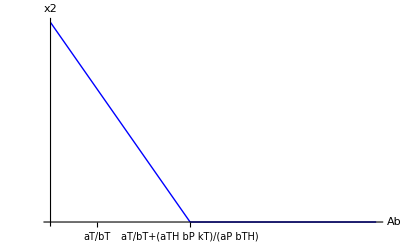

```mathematica
With[{at=1,bt=1, cT=1, ap=1,bp=1,kP=1,kT=1,a1=1,a2=1,a3=1,b1=1,b2=1,b3=1,u=1},
Show[Plot[(b1 b2 u P[t])/(a1 a2 x3[t]^2)/.x3[t]-> 1/3 ((Ab b3 T[t])/a3+(2^(1/3) a1 a2 Ab^2 b3^2 T[t]^2)/(a3 (27 a1^2 a2^2 a3^2 b1 b2 b3 u P[t] T[t]+2 a1^3 a2^3 Ab^3 b3^3 T[t]^3+3 √3 √(27 a1^4 a2^4 a3^4 b1^2 b2^2 b3^2 u^2 P[t]^2 T[t]^2+4 a1^5 a2^5 a3^2 Ab^3 b1 b2 b3^4 u P[t] T[t]^4))^(1/3))+((27 a1^2 a2^2 a3^2 b1 b2 b3 u P[t] T[t]+2 a1^3 a2^3 Ab^3 b3^3 T[t]^3+3 √3 √(27 a1^4 a2^4 a3^4 b1^2 b2^2 b3^2 u^2 P[t]^2 T[t]^2+4 a1^5 a2^5 a3^2 Ab^3 b1 b2 b3^4 u P[t] T[t]^4))^(1/3))/(2^(1/3) a1 a2 a3))/.{T[t]-> 1/((ap at b3)/(a3 bp bt)+kT),P[t]-> (a1 a2 bp^2)/(ap^3 b1 b2 b3 u)(ap b3 (at/bt-Ab)+a3 bp kT)},{Ab,0.5,2},PlotRange->All,PlotStyle->{Blue,Thick}],
Plot[(b1 b2 u P[t])/(a1 a2 x3[t]^2)/.x3[t]-> 1/3 ((Ab b3 T[t])/a3+(2^(1/3) a1 a2 Ab^2 b3^2 T[t]^2)/(a3 (27 a1^2 a2^2 a3^2 b1 b2 b3 u P[t] T[t]+2 a1^3 a2^3 Ab^3 b3^3 T[t]^3+3 √3 √(27 a1^4 a2^4 a3^4 b1^2 b2^2 b3^2 u^2 P[t]^2 T[t]^2+4 a1^5 a2^5 a3^2 Ab^3 b1 b2 b3^4 u P[t] T[t]^4))^(1/3))+((27 a1^2 a2^2 a3^2 b1 b2 b3 u P[t] T[t]+2 a1^3 a2^3 Ab^3 b3^3 T[t]^3+3 √3 √(27 a1^4 a2^4 a3^4 b1^2 b2^2 b3^2 u^2 P[t]^2 T[t]^2+4 a1^5 a2^5 a3^2 Ab^3 b1 b2 b3^4 u P[t] T[t]^4))^(1/3))/(2^(1/3) a1 a2 a3))/.{T[t]-> 1/kT(1-at/(Ab bt)),P[t]-> 0},{Ab,2,4},PlotRange->All,PlotStyle->{Blue,Thick}],
AxesLabel-> {"Ab","x2"},Ticks->{{{1,"aT/bT"},{2,"aT/bT+(aTH bP kT)/(aP bTH)"}},None}]]
```

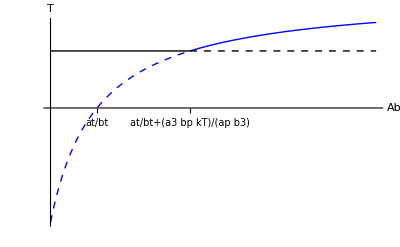
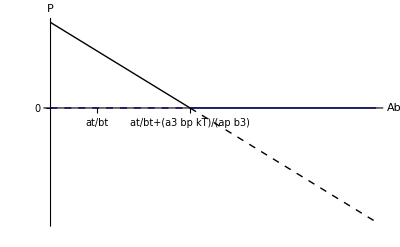
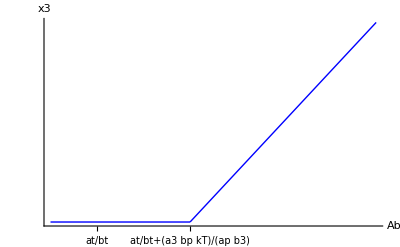
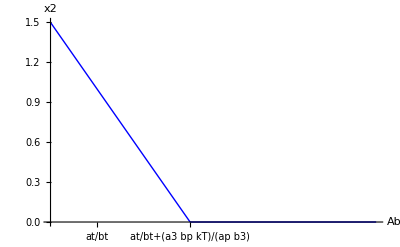
```mathematica
Export["bifurcation plot Ab perturbation.pdf",{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

bifurcation plot Ab perturbation.pdf

## Adding a trans-differentiation term

### Equations for model with trans-differentiation to thyrotrophs

```mathematica
transeq={x1'[t]==-a1 x1[t]+(b1 u)/x3[t],
x2'[t]==-a2 x2[t]+(b2 P[t] x1[t])/x3[t],
x3'[t]==b30+(b3 T[t] (Ab+x2[t]))/(1+kx2 (Ab+x2[t]))-a3 x3[t],
T'[t]==T[t] (-at+(bt (1-kT T[t]) (Ab+x2[t]))/(1+kx2 (Ab+x2[t]))),
P'[t]==P[t] (-ap+(bp (1-kP P[t]))/x3[t])+bpcross/x3[t](1-kP P[t])};
```

### Rescaling equations

```mathematica
rule=Join[#,D[#,t]]&@(#[[1]]->#[[1]]#[[2]]&/@Solve[transeq/.b30|Ab|kT|kP|bpcross|kx2|x_'[t]->0/.bp->1,transeq[[;;,1]]/.x_'[t]->x[t]][[1]])
```

{x1[t]→(ap b1 u x1[t])/a1,x2[t]→(at x2[t])/bt,x3[t]→x3[t]/ap,T[t]→(a3 bt T[t])/(ap at b3),P[t]→(a1 a2 at P[t])/(ap^2 b1 b2 bt u),x1'[t]→(ap b1 u x1'[t])/a1,x2'[t]→(at x2'[t])/bt,x3'[t]→x3'[t]/ap,T'[t]→(a3 bt T'[t])/(ap at b3),P'[t]→(a1 a2 at P'[t])/(ap^2 b1 b2 bt u)}

```mathematica
prule={b30->(a3 B30)/ap,Ab->(AB at)/bt,kx2->(bt KX2)/at,kT->(ap at b3 KT)/(a3 bt),kP->(ap^2 b1 b2 bt KP u)/(a1 a2 at),bpcross->(a1 a2 at BPcross)/(ap^2 b1 b2 bt u)};
```

```mathematica
Thread[(#[[;;,1]])/{a1,a2,a3,at,ap}==FullSimplify@((#[[;;,2]])/{a1,a2,a3,at,ap})]&@((#[[1]])/(#[[1]]/.x_'[t]->1)==(#[[2]])/(#[[1]]/.x_'[t]->1)&/@(transeq/.rule/.prule))
```

{x1'[t]/a1==-x1[t]+1/x3[t],x2'[t]/a2==-x2[t]+(P[t] x1[t])/x3[t],x3'[t]/a3==B30+(T[t] (AB+x2[t]))/(1+AB KX2+KX2 x2[t])-x3[t],T'[t]/at==-(T[t] (1+AB (-1+KX2)+(-1+KX2) x2[t]+KT T[t] (AB+x2[t])))/(1+AB KX2+KX2 x2[t]),P'[t]/ap==(BPcross-P[t] (-bp+BPcross KP+bp KP P[t]+x3[t]))/x3[t]}

```mathematica
scaledeq={1/a1 x1'[t]==1/x3[t]-x1[t],
1/a2 x2'[t]==(P[t] x1[t])/x3[t]-x2[t],
1/a3 x3'[t]==B30+(T[t] (AB+x2[t]))/(1+KX2(AB+x2[t]))-x3[t],
1/at T'[t]==T[t]((AB+x2[t])/(1+KX2(AB+x2[t]))(1-KT T[t])-1),
1/ap P'[t]==(BPcross+bp P[t])/x3[t](1-KP P[t])-P[t]};
```

### x2(x3) relation in trans-differentiation model

```mathematica
x2x3relation=Solve[Refine[Eliminate[scaledeq[[{1,2,5}]]/.x_'[t]->0/.x_[t]->x,{P,x1}],x3>0],x2]//FullSimplify//PowerExpand//FullSimplify
```

{{x2→-(-bp+BPcross KP+x3+√((bp+BPcross KP)^2-2 (bp-BPcross KP) x3+x3^2))/(2 bp KP x3^2)},{x2→(bp-BPcross KP-x3+√((bp+BPcross KP)^2-2 (bp-BPcross KP) x3+x3^2))/(2 bp KP x3^2)}}

```mathematica
x2x3relation/.{BPcross->0,KP->1,bp->1}//FullSimplify//PowerExpand//FullSimplify
```

{{x2→(1-x3)/x3^2},{x2→0}}

```mathematica
x2x3relation[[2,1,2]]/.KP->1
```

(bp-BPcross-x3+√((bp+BPcross)^2-2 (bp-BPcross) x3+x3^2))/(2 bp x3^2)

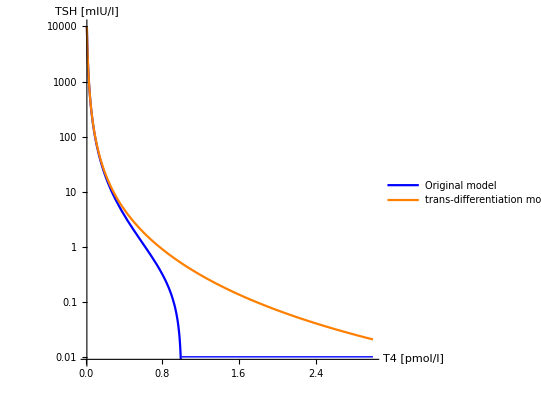

```mathematica
LogPlot[Evaluate[x2x3relation[[2,1,2]]/.KP|bp->1/.{{BPcross->0},{BPcross->.5}}],{x3,0.01,3},PlotStyle->{Blue,Orange}, PlotRange->{0.009,All},Epilog->{Blue, Line[{{1,Log@0.01},{3,Log@0.01}}]},PlotRangePadding->None(*Ticks->{{.5,1,1.5,2,2.5,3},Automatic}*),AxesLabel->{"T4 [pmol/l]", "TSH [mIU/l]"},PlotLegends->{"Original model","trans-differentiation model"},AspectRatio->1]
```

### x3 steady-state depends on the sum bp+bp_cross

Solving x3 st. st. in the simple model, we see that x3 depends on bp and bpcross:

```mathematica
scaledeq/.x_'[t]|B30|AB|KX2|KT|KP->0/.x_[t]->x//.{x1->1/x3,x2->1,P->x3^2,T->x3}
```

{True,True,True,True,0==-x3^2+(BPcross+bp x3^2)/x3}

```mathematica
Solve[0==-x3^2+(BPcross+bp x3^2)/x3,x3][[1]]//FullSimplify
```

{x3→1/3 (bp+bp^2/((bp^3+3/2 (9 BPcross+√3 √(BPcross (4 bp^3+27 BPcross))))^(1/3))+(bp^3+3/2 (9 BPcross+√3 √(BPcross (4 bp^3+27 BPcross))))^(1/3))}

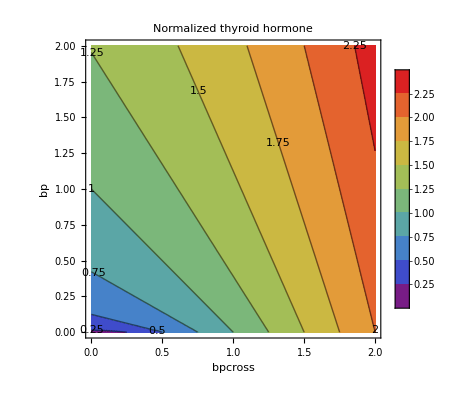

```mathematica
ContourPlot[1/3 (bp+bp^2/((bp^3+3/2 (9 BPcross+√3 √(BPcross (4 bp^3+27 BPcross))))^(1/3))+(bp^3+3/2 (9 BPcross+√3 √(BPcross (4 bp^3+27 BPcross))))^(1/3)),{bp,0,2},{BPcross,0,2},MeshFunctions->{#3&},PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"bpcross","bp"},ContourLabels->All(*(Text[#3,{#1,#2},Background->White]&)*),PlotLabel->"Normalized thyroid hormone"]
```

Even if KP is not equal to zero, the model is not affected much:

```mathematica
scaledeq/.x_'[t]|B30|AB|KX2|KT->0/.x_[t]->x//.{x1->1/x3,x2->1,P->x3^2,T->x3}
```

{True,True,True,True,0==-x3^2+((BPcross+bp x3^2) (1-KP x3^2))/x3}

```mathematica
Manipulate[ContourPlot[Select[NSolve[0==-x3^2+((BPcross+bp x3^2) (1-KP x3^2))/x3,x3,Reals][[;;,1,2]],# >0&][[1]],{bp,0,2},{BPcross,0,2},MeshFunctions->{#3&},PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"bpcross","bp"},ContourLabels->All(*(Text[#3,{#1,#2},Background->White]&)*),PlotLabel->"Normalized thyroid hormone",PerformanceGoal->"Quality",PlotRange->All],{{KP, .5},0,2}]
```

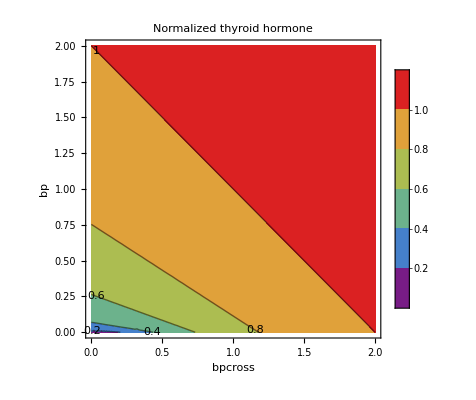

```mathematica
With[{KP=.5},ContourPlot[Select[NSolve[0==-x3^2+((BPcross+bp x3^2) (1-KP x3^2))/x3,x3,Reals][[;;,1,2]],# >0&][[1]],{bp,0,2},{BPcross,0,2},MeshFunctions->{#3&},PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"bpcross","bp"},ContourLabels->All(*(Text[#3,{#1,#2},Background->White]&)*),PlotLabel->"Normalized thyroid hormone",PerformanceGoal->"Quality",PlotRange->All]]
```

```mathematica
Export["trans_differntiation_x3_stst.pdf",{-Graphics-,-Graphics-}]
```

trans_differntiation_x3_stst.pdf

### Nullclines and stream plot for the trans-differntiation model

```mathematica
sloweq=scaledeq/.x1'[t]|x2'[t]|x3'[t]|KX2|B30|AB->0/.{x1[t]->1/(P[t] T[t])^(1/3),x2[t]->P[t]/(((P[t] T[t])^(1/3))^2),x3[t]->(P[t] T[t])^(1/3)}/.x_[t]->x//PowerExpand
```

{True,True,True,T'/at==T (-1+(P^(1/3) (1-KT T))/T^(2/3)),P'/ap==-P+((BPcross+bp P) (1-KP P))/(P^(1/3) T^(1/3))}

```mathematica
FullSimplify[0==-P+((BPcross+bp P) (1-KP P))/(P^(1/3) T^(1/3))]
```

P==((BPcross+bp P) (1-KP P))/(P^(1/3) T^(1/3))

```mathematica
Manipulate[
Show[{
StreamPlot[{T (-1+(P^(1/3) (1-KT T))/T^(2/3)),-P+((BPcross+bp P) (1-KP P))/(P^(1/3) T^(1/3))},{T,0,2},{P,0,2},PerformanceGoal->"Quality",StreamStyle->Blend[{Blue,White},.75],StreamColorFunction->None],
ContourPlot[{P^(1/3) (1-KT T)==T^(2/3),T==0,(BPcross+bp P) (1-KP P)==P^(4/3) T^(1/3)},{T,-0.1,2},{P,0,2},PerformanceGoal->"Quality",ContourStyle->{{Thick,Orange},{Thick,Orange},{Thick,Blue}}]},FrameLabel->{"T","P"},PlotLabel-> "bp="<>ToString@bp<>", BPcross="<>ToString@BPcross],
{BPcross,0,10},{{bp,1},0,10},{{KT,0},0,1},{{KP,0},0,1}]
```

```mathematica
fig[1,bp_,KT_,KP_]
```

```mathematica
parametersets={{BPcross-> 0,bp-> 1,KT->1,KP->1},{BPcross-> 0.5,bp-> 0.5,KT->1,KP->1},{BPcross-> 1,bp-> 0,KT->1,KP->1}}
```

{{BPcross→0,bp→1,KT→1,KP→1},{BPcross→0.5,bp→0.5,KT→1,KP→1},{BPcross→1,bp→0,KT→1,KP→1}}

```mathematica
fig[BPcross_,bp_,KT_,KP_]:=Show[{
StreamPlot[{T (-1+(P^(1/3) (1-KT T))/T^(2/3)),-P+((BPcross+bp P) (1-KP P))/(P^(1/3) T^(1/3))},{T,0,1},{P,0,1},PerformanceGoal->"Quality",StreamStyle->Blend[{Blue,White},.75],StreamColorFunction->None],
ContourPlot[{P^(1/3) (1-KT T)==T^(2/3),T==0,(BPcross+bp P) (1-KP P)==P^(4/3) T^(1/3)},{T,-0.1,1},{P,0,1},PerformanceGoal->"Quality",ContourStyle->{{Thick,Orange},{Thick,Orange},{Thick,Blue}}]},FrameLabel->{"T","P"},PlotLabel-> "bp="<>ToString@bp<>", bpcross="<>ToString@BPcross]
```

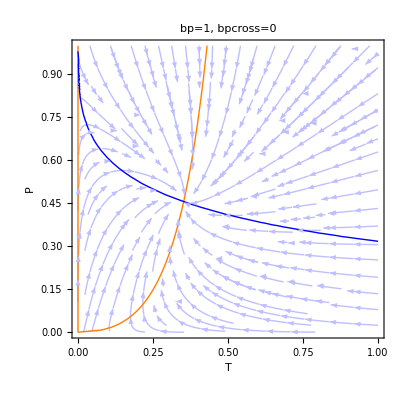
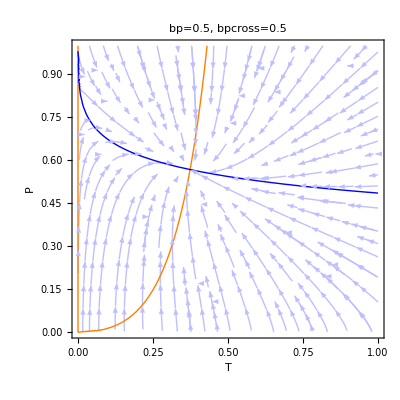
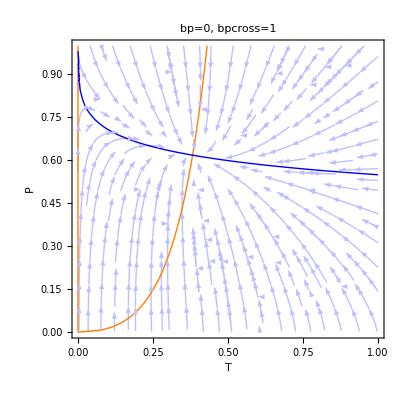

```mathematica
Table[fig@@parametersets[[i,;;,2]],{i,1,Length@parametersets}]
```

```mathematica
Export["trans_differntiation_nullclines.pdf",{-Graphics-,-Graphics-,-Graphics-}]
```

trans_differntiation_nullclines.pdf